# Title

Author Name

Abstract

## Section

A 150-g ball at the end of a string is revolving uniformly in a horizontal circle of radius 0.600 m, as in Fig. 5–1 or 5–3. The ball makes 2.00 revolutions in a second. What is its centripetal acceleration?

If the ball makes 2.00 complete revolutions per second, then the ball travels in a complete circle in a time interval equal to 0.500 s, which is its period T. The distance traveled in this time is the circumference of the circle, 2π r, where r is the radius of the circle. Therefore, the ball has speed:

```mathematica
FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
v | linear velocity | LinearSpeed | {{LengthUnit,1},{TimeUnit,-1}}
n | rotation rate | RevolutionRate | {TimeUnit,-1}
r | radius | Radius | {LengthUnit,1}

```mathematica
FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"}]
```

v LinearSpeed==(2 π /rev) n RevolutionRate r Radius

```mathematica
FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"}]/.<|"r" "Radius"->Quantity[600, "Millimeters"],"n" "RevolutionRate"->Quantity[2, 1/("Seconds")]|>
```

v LinearSpeed==2400 π mm/(s rev)

```mathematica
N[FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"}]/.<|"r" "Radius"->Quantity[600, "Millimeters"],"n" "RevolutionRate"->Quantity[2, 1/("Seconds")]|>]
```

v LinearSpeed==7539.82 mm/(s rev)

```mathematica
UnitDimensions[Quantity[7539.822368615503, ("Millimeters")/("Revolutions" "Seconds")]]
```

{{LengthUnit,1},{RevolutionUnit,-1},{TimeUnit,-1}}

```mathematica
Cases[q_/;ContainsAll[{{"LengthUnit",1},{"TimeUnit",-1}}][UnitDimensions[q]]->UnitConvert[q]][N[FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"}]/.<|"r" "Radius"->Quantity[600, "Millimeters"],"n" "RevolutionRate"->Quantity[2, 1/("Seconds")]|>]]
```

{7.53982 m/(s rev)}

```mathematica
Cases[q_/;ContainsAll[{{"LengthUnit",1},{"TimeUnit",-1}}][UnitDimensions[q]]->UnitConvert[q]][FormulaData[{"AngularToLinearVelocity","RotationRate","Radius"}]/.<|"r" "Radius"->Quantity[600, "Millimeters"],"n" "RevolutionRate"->Quantity[2, 1/("Seconds")]|>]
```

{(12 π)/5 m/(s rev)}

```mathematica
CentripetalAccelerationFormulas=FormulaLookup["*CentripetalAcceleration*"]
```

{{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,OrbitSpeed},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,RotationSpeed},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance},{GravitationalAcceleration,Radius},{Weight,GravitationalAcceleration},{Weight,StandardGravitationalAcceleration},{BarometricFormula,MassDensity,GravitationalAcceleration},{BarometricFormula,Pressure,GravitationalAcceleration},{GravitationalAcceleration,Radius,Height},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration},{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance},{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance},AccelerationNumber,{BoussinesqApproximationParameter,ApproximatedAccelerationOfGravity},{DistanceSpeedTime,Acceleration},{DistanceSpeedTimeCircularForm,AngularAcceleration},{SpeedAccelerationDistance,Distance},{SpeedAccelerationDistanceCircularForm,AngularDisplacement},{SpeedAccelerationTime,DeltaSpeed},{SpeedAccelerationTime,InitialSpeed},{SpeedAccelerationTime,NoInitialSpeed},{SpeedAccelerationTimeCircularForm,InitialAngularSpeed},{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed},{Work,Acceleration},{DistanceSpeedTime,Acceleration,InitialPosition},{DistanceSpeedTime,Acceleration,InitialSpeed},{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration},{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration},{SpeedAccelerationDistance,InitialPosition,FinalPosition},{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle},{Torque,AngularAcceleration,MomentOfInertia},{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition},{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration},{CentripetalForce,AngularVelocity},{CentripetalForce,RotationSpeed},AcceleratingFrequency}

```mathematica
AssociationMap[Dataset[<|"Description"->FormulaData[#,"QuantityVariableNames"],"Formula"->FormulaData[#,"Formula"]|>]&][CentripetalAccelerationFormulas]
```

<|{CentripetalAcceleration,AngularVelocity}→,{CentripetalAcceleration,OrbitSpeed}→,{CentripetalAcceleration,RotationRate}→,{CentripetalAcceleration,RotationSpeed}→,{CentripetalAcceleration,AngularVelocity,Diameter}→,{CentripetalAcceleration,AngularVelocity,OrbitDistance}→,{CentripetalAcceleration,OrbitSpeed,Diameter}→,{CentripetalAcceleration,OrbitSpeed,Radius}→,{CentripetalAcceleration,RotationRate,Diameter}→,{CentripetalAcceleration,RotationRate,OrbitDistance}→,{CentripetalAcceleration,RotationSpeed,Diameter}→,{CentripetalAcceleration,RotationSpeed,OrbitDistance}→,{GravitationalAcceleration,Radius}→,{Weight,GravitationalAcceleration}→,{Weight,StandardGravitationalAcceleration}→,{BarometricFormula,MassDensity,GravitationalAcceleration}→,{BarometricFormula,Pressure,GravitationalAcceleration}→,{GravitationalAcceleration,Radius,Height}→,{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration}→,{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration}→,{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration}→,{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration}→,{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance}→,{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance}→,{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance}→,{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance}→,AccelerationNumber→,{BoussinesqApproximationParameter,ApproximatedAccelerationOfGravity}→,{DistanceSpeedTime,Acceleration}→,{DistanceSpeedTimeCircularForm,AngularAcceleration}→,{SpeedAccelerationDistance,Distance}→,{SpeedAccelerationDistanceCircularForm,AngularDisplacement}→,{SpeedAccelerationTime,DeltaSpeed}→,{SpeedAccelerationTime,InitialSpeed}→,{SpeedAccelerationTime,NoInitialSpeed}→,{SpeedAccelerationTimeCircularForm,InitialAngularSpeed}→,{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed}→,{Work,Acceleration}→,{DistanceSpeedTime,Acceleration,InitialPosition}→,{DistanceSpeedTime,Acceleration,InitialSpeed}→,{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration}→,{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration}→,{SpeedAccelerationDistance,InitialPosition,FinalPosition}→,{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle}→,{Torque,AngularAcceleration,MomentOfInertia}→,{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition}→,{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration}→,{CentripetalForce,AngularVelocity}→,{CentripetalForce,RotationSpeed}→,AcceleratingFrequency→|>

```mathematica
FormulaData[{"CentripetalAcceleration","AngularVelocity"},"QuantityVariableNames"]
```

{a Acceleration→centripetal acceleration,r Radius→radius,ω AngularVelocity→angular velocity}

```mathematica
AssociationMap[Dataset[<|"Description"->FormulaData[#,"QuantityVariableNames"],"Formula"->FormulaData[#,"Formula"]|>]&][FormulaLookup["*CentripetalAcceleration*RotationRate*"]]
```

<|{CentripetalAcceleration,RotationRate}→,{CentripetalAcceleration,RotationRate,Diameter}→,{CentripetalAcceleration,RotationRate,OrbitDistance}→,{CentripetalAcceleration,RotationSpeed}→,{CentripetalAcceleration,RotationSpeed,Diameter}→,{CentripetalAcceleration,RotationSpeed,OrbitDistance}→,{CentripetalAcceleration,AngularVelocity}→,{CentripetalAcceleration,OrbitSpeed}→,{CentripetalAcceleration,AngularVelocity,Diameter}→,{CentripetalAcceleration,AngularVelocity,OrbitDistance}→,{CentripetalAcceleration,OrbitSpeed,Diameter}→,{CentripetalAcceleration,OrbitSpeed,Radius}→,{GravitationalAcceleration,Radius}→,{Weight,GravitationalAcceleration}→,{Weight,StandardGravitationalAcceleration}→,{BarometricFormula,MassDensity,GravitationalAcceleration}→,{BarometricFormula,Pressure,GravitationalAcceleration}→,{GravitationalAcceleration,Radius,Height}→,{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration}→,{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration}→,{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration}→,{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration}→,{InclinedPlaneRolling,PureRolling,Slope,MomentOfInertia,GravitationalAcceleration,SpeedDistance}→,{InclinedPlaneRolling,PureRolling,Slope,ShapeFactor,GravitationalAcceleration,SpeedDistance}→,{InclinedPlaneRolling,PureRolling,SlopeAngle,MomentOfInertia,GravitationalAcceleration,SpeedDistance}→,{InclinedPlaneRolling,PureRolling,SlopeAngle,ShapeFactor,GravitationalAcceleration,SpeedDistance}→,AccelerationNumber→,{BoussinesqApproximationParameter,ApproximatedAccelerationOfGravity}→,{DistanceSpeedTime,Acceleration}→,{DistanceSpeedTimeCircularForm,AngularAcceleration}→,{SpeedAccelerationDistance,Distance}→,{SpeedAccelerationDistanceCircularForm,AngularDisplacement}→,{SpeedAccelerationTime,DeltaSpeed}→,{SpeedAccelerationTime,InitialSpeed}→,{SpeedAccelerationTime,NoInitialSpeed}→,{SpeedAccelerationTimeCircularForm,InitialAngularSpeed}→,{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed}→,{Work,Acceleration}→,{AngularToLinearVelocity,RotationRate,Diameter}→,{AngularToLinearVelocity,RotationRate,OrbitDistance}→,{AngularToLinearVelocity,RotationRate,Radius}→,{DistanceSpeedTime,Acceleration,InitialPosition}→,{DistanceSpeedTime,Acceleration,InitialSpeed}→,{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration}→,{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration}→,{SpeedAccelerationDistance,InitialPosition,FinalPosition}→,{SpeedAccelerationDistanceCircularForm,InitialAngle,FinalAngle}→,{Torque,AngularAcceleration,MomentOfInertia}→,{DistanceSpeedTime,Acceleration,InitialSpeed,InitialPosition}→,{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration}→,{CentripetalForce,AngularVelocity}→,{CentripetalForce,RotationSpeed}→,AcceleratingFrequency→,RotationalKineticEnergy→,RotationalPower→,{SpecificRotation,PureLiquid}→,{SpecificRotation,Solution}→|>

```mathematica
FormulaData[{"CentripetalAcceleration","RotationRate"}]
```

a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 r Radius

```mathematica
FormulaData[{"CentripetalAcceleration","RotationRate"},"QuantityVariables"]
```

{a Acceleration,n RevolutionRate,r Radius}

```mathematica
FormulaData[{"CentripetalAcceleration","RotationRate"},"QuantityVariableNames"]
```

{a Acceleration→centripetal acceleration,n RevolutionRate→rotation rate,r Radius→radius}

```mathematica
FormulaData[{"CentripetalAcceleration","RotationRate"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
a | centripetal acceleration | Acceleration | {{LengthUnit,1},{TimeUnit,-2}}
n | rotation rate | RevolutionRate | {TimeUnit,-1}
r | radius | Radius | {LengthUnit,1}

```mathematica
FormulaData[{"CentripetalAcceleration","RotationRate"}]/.<|"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]|>
```

a Acceleration==9600 π^2 mm/(s^2 rev^2)

```mathematica
N[FormulaData[{"CentripetalAcceleration","RotationRate"}]/.<|"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]|>]
```

a Acceleration==94748.2 mm/(s^2 rev^2)

```mathematica
N[FormulaData[{"CentripetalAcceleration","RotationRate"}]/.<|"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]|>]/.{q_?QuantityQ/;ContainsAll[{{"LengthUnit",1},{"TimeUnit",-2}}][UnitDimensions[q]]->UnitConvert[q,"SIBase"]}
```

a Acceleration==94.7482 m/(s^2 rev^2)

```mathematica
FormulaData[{"CentripetalAcceleration","RotationRate"},<|"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]|>]
```

a Acceleration==9600 π^2 mm/(s^2 rev^2)

```mathematica
FormulaData[{"CentripetalAcceleration","RotationRate"},{"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]}]//Quiet
```

a Acceleration==9600 π^2 mm/(s^2 rev^2)

```mathematica
N[FormulaData[{"CentripetalAcceleration","RotationRate"},{"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]}]//Quiet]
```

a Acceleration==94748.2 mm/(s^2 rev^2)

```mathematica
N[FormulaData[{"CentripetalAcceleration","RotationRate"},{"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]}]//Quiet]/.{q_?QuantityQ/;ContainsAll[{{"LengthUnit",1},{"TimeUnit",-2}}][UnitDimensions[q]]->UnitConvert[q,"SIBase"]}
```

a Acceleration==94.7482 m/(s^2 rev^2)

```mathematica
Quiet[FormulaData[{"CentripetalAcceleration","RotationRate"},{"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]}]]/.{q_?QuantityQ/;ContainsAll[{{"LengthUnit",1},{"TimeUnit",-2}}][UnitDimensions[q]]->UnitConvert[q,"SIBase"]}
```

a Acceleration==(48 π^2)/5 m/(s^2 rev^2)

```mathematica
Quiet[Quiet[FormulaData[{"CentripetalAcceleration","RotationRate"},{"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]}]]/.{q_?QuantityQ/;ContainsAll[{{"LengthUnit",1},{"TimeUnit",-2}}][UnitDimensions[q]]->UnitConvert[q,"SI"]}]
```

a Acceleration==9600 π^2 mm/(s^2 rev^2)

```mathematica
Quiet[Quiet[FormulaData[{"CentripetalAcceleration","RotationRate"},{"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]}]]/.{q_?QuantityQ->UnitConvert[q,"SI"]}]
```

a Acceleration==9600 π^2 mm/(s^2 rev^2)

```mathematica
Quiet[Quiet[FormulaData[{"CentripetalAcceleration","RotationRate"},{"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]}]]/.{q_?QuantityQ->UnitConvert[q,"SIBase"]}]
```

a Acceleration==(48 π^2)/5 m/(s^2 rev^2)

```mathematica
N[Quiet[Quiet[FormulaData[{"CentripetalAcceleration","RotationRate"},{"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[600, "Millimeters"]}]]/.{q_?QuantityQ->UnitConvert[q,"SIBase"]}]]
```

a Acceleration==94.7482 m/(s^2 rev^2)

```mathematica
N[FormulaData[{"CentripetalAcceleration","RotationRate"}]/.<|"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[1.2, "Meters"]|>]/.{q_?QuantityQ/;ContainsAll[{{"LengthUnit",1},{"TimeUnit",-2}}][UnitDimensions[q]]->UnitConvert[q,"SIBase"]}
```

a Acceleration==189.496 m/(s^2 rev^2)

```mathematica
/
```

(a Acceleration==189.496 m/(s^2 rev^2))/(a Acceleration==94.7482 m/(s^2 rev^2))

```mathematica
///FullSimplify
```

(a Acceleration==189.496 m/(s^2 rev^2))/(a Acceleration==94.7482 m/(s^2 rev^2))

```mathematica
DivideSides[,]
```

Piecewise[{{False, a Acceleration≠0}, {a Acceleration==94.7482 m/(s^2 rev^2), True}}]

```mathematica
DivideSides[,Last[]]
```

Piecewise[{{(0.00527714 s^2 rev^2/m) a Acceleration==0.5, 189.496 m/(s^2 rev^2)≠0}, {a Acceleration==94.7482 m/(s^2 rev^2), True}}]

```mathematica
DivideSides[,Last[]]
```

Piecewise[{{(0.0105543 s^2 rev^2/m) a Acceleration==2., 94.7482 m/(s^2 rev^2)≠0}, {a Acceleration==189.496 m/(s^2 rev^2), True}}]

```mathematica
FormulaLookup["*CentripetalForce*"]
```

{{CentripetalForce,AngularVelocity},{CentripetalForce,RotationSpeed},{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,OrbitSpeed},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,RotationSpeed},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance}}

```mathematica
FormulaData[{"CentripetalForce","AngularVelocity"}]
```

F Force==(1 per radian^2) m Mass r Radius (ω AngularVelocity)^2

```mathematica
FormulaData[{"CentripetalForce","RotationSpeed"}]
```

F Force==(m Mass (v Speed)^2)/(r Radius)

```mathematica
FormulaData[{"CentripetalAcceleration", "RotationRate"}]
```

a Acceleration==(4 π^2 /rev^2) (n RevolutionRate)^2 r Radius

```mathematica
CentripetalForceRotationRate="F" "Force"=="m" "Mass"(Quantity[4 π^2, 1/("Revolutions")^2]) ("n" "RevolutionRate")^2 "r" "Radius"
```

F Force==(4 π^2 /rev^2) m Mass (n RevolutionRate)^2 r Radius

```mathematica
CentripetalForceRotationRate/.<|"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[0.6, "Meters"],"m" "Mass"->Quantity[150, "Grams"]|>
```

F Force==14212.2 g m/(s^2 rev^2)

```mathematica
CentripetalForceRotationRate/.<|"n" "RevolutionRate"->Quantity[2, 1/("Seconds")],"r" "Radius"->Quantity[0.6, "Meters"],"m" "Mass"->Quantity[150, "Grams"]|>/.{q_?QuantityQ->UnitConvert[q,"SIBase"]}
```

F Force==14.2122 kg m/(s^2 rev^2)

```mathematica
AssociationMap[FormulaData][{{"Weight","GravitationalAcceleration"},{"Weight","StandardGravitationalAcceleration"},{"WeightOnMassiveBodies","Height"},{"WeightOnMassiveBodies","Surface"}}]
```

<|{Weight,GravitationalAcceleration}→W Weight==g GravitationalAcceleration m Mass,{Weight,StandardGravitationalAcceleration}→W Weight==( g) m Mass,{WeightOnMassiveBodies,Height}→W Force==(( G) m Mass M Mass)/(h Height+r Radius)^2,{WeightOnMassiveBodies,Surface}→W Force==(( G) m Mass M Mass)/(r Radius)^2|>

```mathematica
FormulaData[{"Weight","StandardGravitationalAcceleration"},{"m" "Mass"->Quantity[150, "Grams"]}]
```

W Weight==588399/400000 N

```mathematica
N[FormulaData[{"Weight","StandardGravitationalAcceleration"},{"m" "Mass"->Quantity[150, "Grams"]}]]
```

W Weight==1.471 N

```mathematica
FormulaLookup["Weight"]
```

{WeightedAverageCostOfCapital,{BaseballWeightedOnBaseAverage,HitByPitch},{BaseballWeightedOnBaseAverage,ReachedBaseOnError},{BaseballWeightedOnBaseAverage,Standard},{EquivalentDoseOfIonizingRadiation,RadiationWeightingFactor},{Weight,GravitationalAcceleration},{Weight,StandardGravitationalAcceleration},{WeightOnMassiveBodies,Height},{WeightOnMassiveBodies,Surface},{WeightTrainingExerciseEnergyExpenditure,Averaged},{WeightTrainingExerciseEnergyExpenditure,Female},{WeightTrainingExerciseEnergyExpenditure,Male},{BaseballWeightedOnBaseAverage,ReachedBaseOnError,HitByPitch}}

```mathematica
FormulaLookup["CentripetalAcceleration"]
```

{{CentripetalAcceleration,RotationSpeed},{CentripetalAcceleration,AngularVelocity},{CentripetalAcceleration,AngularVelocity,Diameter},{CentripetalAcceleration,AngularVelocity,OrbitDistance},{CentripetalAcceleration,OrbitSpeed},{CentripetalAcceleration,OrbitSpeed,Diameter},{CentripetalAcceleration,OrbitSpeed,Radius},{CentripetalAcceleration,RotationRate},{CentripetalAcceleration,RotationRate,Diameter},{CentripetalAcceleration,RotationRate,OrbitDistance},{CentripetalAcceleration,RotationSpeed,Diameter},{CentripetalAcceleration,RotationSpeed,OrbitDistance}}

```mathematica
FormulaData[{"CentripetalAcceleration","RotationSpeed"}]
```

a Acceleration==(v Speed)^2/(r Radius)

```mathematica
FormulaData[{"CentripetalAcceleration","RotationSpeed"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
a | centripetal acceleration | Acceleration | {{LengthUnit,1},{TimeUnit,-2}}
r | radius | Radius | {LengthUnit,1}
v | tangential speed | Speed | {{LengthUnit,1},{TimeUnit,-1}}

```mathematica
FormulaData[{"Weight","GravitationalAcceleration"},"QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
W | weight | Weight | {{LengthUnit,1},{MassUnit,1},{TimeUnit,-2}}
g | gravitational acceleration | GravitationalAcceleration | {{LengthUnit,1},{TimeUnit,-2}}
m | mass | Mass | {MassUnit,1}

```mathematica
VerticalCircleCentripetalForce="m" "Mass" ("v" "Speed")^2/("r" "Radius")Sin["θ" "Angle"]+"m" "Mass"("g" "GravitationalAcceleration")=="F" "Force"
```

g GravitationalAcceleration m Mass+(m Mass (v Speed)^2 Sin[θ Angle])/(r Radius)==F Force

```mathematica
VerticalCircleCentripetalForce/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"]|>
```

1469.93 g m/s^2+(136.364 g/m) (v Speed)^2 Sin[θ Angle]==F Force

```mathematica
VerticalCircleCentripetalForce/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"],"F" "Force"->Quantity[0, "Newtons"]|>
```

1469.93 g m/s^2+(136.364 g/m) (v Speed)^2 Sin[θ Angle]==0 N

```mathematica
VerticalCircleCentripetalForce/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"],"F" "Force"->Quantity[0, "Newtons"],"θ" "Angle"->90Degree|>
```

1469.93 g m/s^2+(136.364 g/m) (v Speed)^2==0 N

```mathematica
Solve[VerticalCircleCentripetalForce/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"],"F" "Force"->Quantity[0, "Newtons"],"θ" "Angle"->Pi/2|>,"v" "Velocity"]
```

{}

```mathematica
Solve[VerticalCircleCentripetalForce,"v" "Speed"]
```

SolveValues[g GravitationalAcceleration m Mass+(m Mass (v Speed)^2 Sin[θ Angle])/(r Radius)==F Force,v Speed]

```mathematica
SolveValues["g" "GravitationalAcceleration" "m" "Mass"+("m" "Mass" ("v" "Speed")^2 Sin[t])/("r" "Radius")=="F" "Force","v" "Speed"]
```

{-(√Csc[t] √(F Force-g GravitationalAcceleration m Mass) √(r Radius))/(√(m Mass)),(√Csc[t] √(F Force-g GravitationalAcceleration m Mass) √(r Radius))/(√(m Mass))}

```mathematica
SolveValues["g" "GravitationalAcceleration" "m" "Mass"+("m" "Mass" ("v" "Speed")^2 Sin[t])/("r" "Radius")=="F" "Force"/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->-GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"],"F" "Force"->Quantity[0, "Newtons"],t->Pi/2|>,"v" "Speed"]
```

{-3.28321 m/s,3.28321 m/s}

```mathematica
SelectFirst[Element[QuantityMagnitude[#],]&][SolveValues["g" "GravitationalAcceleration" "m" "Mass"+("m" "Mass" ("v" "Speed")^2 Sin[t])/("r" "Radius")=="F" "Force"/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->-GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"],"F" "Force"->Quantity[0, "Newtons"],t->Pi/2|>,"v" "Speed"]]
```

3.28321 m/s

```mathematica
GeogravityModelData["Magnitude"]
```

9.79952 m/s^2

6.56642 m/s

```mathematica
SolveValues["g" "GravitationalAcceleration" "m" "Mass"+("m" "Mass" ("v" "Speed")^2 Sin[t])/("r" "Radius")=="F" "Force"/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->-GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"],"v" "Speed"->,t->3 Pi/2|>,"F" "Force"]
```

{-7349.64 mN}

```mathematica
UnitConvert[SolveValues["g" "GravitationalAcceleration" "m" "Mass"+("m" "Mass" ("v" "Speed")^2 Sin[t])/("r" "Radius")=="F" "Force"/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->-GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"],"v" "Speed"->,t->3 Pi/2|>,"F" "Force"],"SIBase"]
```

{-7.34964 kg m/s^2}

```mathematica
UnitConvert[SolveValues["g" "GravitationalAcceleration" "m" "Mass"+("m" "Mass" ("v" "Speed")^2 Sin[t])/("r" "Radius")=="F" "Force"/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->-GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"],"v" "Speed"->,t->3 Pi/2|>,"F" "Force"],"SI"]
```

{-7.34964 N}

```mathematica
SolveValues["g" "GravitationalAcceleration" "m" "Mass"+("m" "Mass" ("v" "Speed")^2 Sin[t])/("r" "Radius")=="F" "Force"/.<|"m" "Mass"->Quantity[150, "Grams"],"g" "GravitationalAcceleration"->GeogravityModelData["Magnitude"],"r" "Radius"->Quantity[1.1, "Meters"],"F" "Force"->Quantity[0, "Newtons"],t->Pi/2|>,"v" "Speed"]
```

{(0.-3.28321 ⅈ) m/s,(0.+3.28321 ⅈ) m/s}

```mathematica
Sin[Pi/2]
```

1

```mathematica
Sin[(3Pi)/2]
```

-1

```mathematica
SolveValues["g" "GravitationalAcceleration" "m" "Mass"+("m" "Mass" ("v" "Speed")^2 Sin["α" "Angle"])/("r" "Radius")=="F" "Force","v" "Speed"]
```

SolveValues[g GravitationalAcceleration m Mass+(m Mass (v Speed)^2 Sin[α Angle])/(r Radius)==F Force,v Speed]

```mathematica
Quantity[1469.927763250467, ("Grams" "Meters")/("Seconds")^2]+(Quantity[136.36363636363635, ("Grams")/("Meters")])
```

136.364 g/m+1469.93 g m/s^2

```mathematica
FormulaData["LawOfSines"]
```

Sin[α Angle]/(a Length)==Sin[β Angle]/(b Length)

```mathematica
FormulaData["LawOfSines","QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
a | first side length | Length | {LengthUnit,1}
α | angle opposite first side | Angle | {AngleUnit,1}
b | second side length | Length | {LengthUnit,1}
β | angle opposite second side | Angle | {AngleUnit,1}

## *5-4 Nonuniform Circular Motion

### 25*(II) A car at the Indianapolis 500 accelerates uniformly from the pit area, going from rest to 270 km/h in a semicircular arc with a radius of 220 m. Determine the tangential and radial acceleration of the car when it is halfway through the arc, assuming constant tangential acceleration. If the curve were flat, what coefficient of static friction would be necessary between the tires and the road to provide this acceleration with no slipping or skidding?

```mathematica
eqn="a" "Acceleration"==√((Subscript["a", "c"] "CentripetalAcceleration")^2+(Subscript["a", "tan"] "TangentialAcceleration")^2)
```

a Acceleration==√((a_c CentripetalAcceleration)^2+(a_tan TangentialAcceleration)^2)

```mathematica
eqnWithDifferentSymbolForTangentialAcceleration="a" "Acceleration"==√((Subscript["a", "c"] "CentripetalAcceleration")^2+("a" "TangentialAcceleration")^2)
```

a Acceleration==√((a TangentialAcceleration)^2+(a_c CentripetalAcceleration)^2)

```mathematica
centripetalAcceleration=Subscript["a", "c"] "CentripetalAcceleration"==(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")
```

a_c CentripetalAcceleration==(v_Q Velocity)^2/(r RadiusOfCurvature)

```mathematica
Solve[centripetalAcceleration,Subscript["a", "c"] "CentripetalAcceleration"]
```

{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}

```mathematica
eqn/.<|Subscript["a", "c"] "CentripetalAcceleration"->(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")|>
```

a Acceleration==√((a_tan TangentialAcceleration)^2+(v_Q Velocity)^4/(r RadiusOfCurvature)^2)

I never noticed that the symbol for norm "‖

```mathematica
firstEquation=(Subscript["v", "R"] "Velocity")^2==(Subscript["v", "p"] "Velocity")^2+2("a" "TangentialAcceleration")("\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength")
```

(v_R Velocity)^2==2 a TangentialAcceleration TraditionalForm`‖PR‖ ArcLength+(v_p Velocity)^2

```mathematica
Solve[firstEquation,"a" "TangentialAcceleration"]
```

{{a TangentialAcceleration→-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)}}

```mathematica
secondEquation=(Subscript["v", "Q"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2("a" "TangentialAcceleration")("‖PQ‖" "ArcLength")
```

(v_Q Velocity)^2==2 a TangentialAcceleration ‖PQ‖ ArcLength+(v_P Velocity)^2

```mathematica
Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]
```

{{v_Q Velocity→√(2 a TangentialAcceleration ‖PQ‖ ArcLength+(v_P Velocity)^2)}}

```mathematica
Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]
```

{{v_Q Velocity→√(2 a TangentialAcceleration ‖PQ‖ ArcLength+(v_P Velocity)^2)},{a TangentialAcceleration→-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)}}

```mathematica
Association[Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]]
```

<|v_Q Velocity→√(2 a TangentialAcceleration ‖PQ‖ ArcLength+(v_P Velocity)^2),a TangentialAcceleration→-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)|>

```mathematica
eqn/.<|Subscript["a", "c"] "CentripetalAcceleration"->(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")|>//.Association[Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]]
```

a Acceleration==√((a_tan TangentialAcceleration)^2+(((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)))^2)/(r RadiusOfCurvature)^2)

```mathematica
eqnWithDifferentSymbolForTangentialAcceleration/.<|Subscript["a", "c"] "CentripetalAcceleration"->(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")|>//.Association[Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]]
```

a Acceleration==√((-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength))^2+(((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)))^2)/(r RadiusOfCurvature)^2)

```mathematica
MapAt[FullSimplify,eqnWithDifferentSymbolForTangentialAcceleration/.<|Subscript["a", "c"] "CentripetalAcceleration"->(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")|>//.Association[Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]],2]
```

a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_p Velocity)^2-(v_R Velocity)^2)^2+4 (TraditionalForm`‖PR‖ ArcLength (v_P Velocity)^2+‖PQ‖ ArcLength (-(v_p Velocity)^2+(v_R Velocity)^2))^2)/((r RadiusOfCurvature)^2 (TraditionalForm`‖PR‖ ArcLength)^2))

```mathematica
ExpressionTree[eqnWithDifferentSymbolForTangentialAcceleration/.<|Subscript["a", "c"] "CentripetalAcceleration"->(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")|>//.Association[Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]]]
```

-Graphics-

```mathematica
MapAt[FullSimplify,eqnWithDifferentSymbolForTangentialAcceleration/.<|Subscript["a", "c"] "CentripetalAcceleration"->(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")|>//.Association[Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]],2]
```

```mathematica
Association[Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]]
```

<|v_Q Velocity→√(2 a TangentialAcceleration ‖PQ‖ ArcLength+(v_P Velocity)^2),a TangentialAcceleration→-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)|>

```mathematica
Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]
```

{{v_Q Velocity→√(2 a TangentialAcceleration ‖PQ‖ ArcLength+(v_P Velocity)^2)},{a TangentialAcceleration→-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)}}

```mathematica
Flatten[Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"]]]
```

{v_Q Velocity→√(2 a TangentialAcceleration ‖PQ‖ ArcLength+(v_P Velocity)^2),a TangentialAcceleration→-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)}

```mathematica
Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"],2]
```

{{v_Q Velocity→√(2 a TangentialAcceleration ‖PQ‖ ArcLength+(v_P Velocity)^2),a TangentialAcceleration→-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)}}

```mathematica
eqnWithDifferentSymbolForTangentialAcceleration/.<|Subscript["a", "c"] "CentripetalAcceleration"->(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")|>//.Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"],2]
```

{a Acceleration==√((-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength))^2+(((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)))^2)/(r RadiusOfCurvature)^2)}

```mathematica
MapAt[FullSimplify,eqnWithDifferentSymbolForTangentialAcceleration/.<|Subscript["a", "c"] "CentripetalAcceleration"->(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")|>//.Join[Solve[secondEquation,Subscript["v", "Q"] "Velocity",,Assumptions->{"a" "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],Solve[firstEquation,"a" "TangentialAcceleration"],2],{1,2}]
```

{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_p Velocity)^2-(v_R Velocity)^2)^2+4 (TraditionalForm`‖PR‖ ArcLength (v_P Velocity)^2+‖PQ‖ ArcLength (-(v_p Velocity)^2+(v_R Velocity)^2))^2)/((r RadiusOfCurvature)^2 (TraditionalForm`‖PR‖ ArcLength)^2))}

#### Redoing the problem:

```mathematica
NONUNIFORMCIRCULARMOTIONEQUATION="a" "Acceleration"==√((Subscript["a", "c"] "CentripetalAcceleration")^2+(Subscript["a", "tan"] "TangentialAcceleration")^2)
```

a Acceleration==√((a_c CentripetalAcceleration)^2+(a_tan TangentialAcceleration)^2)

```mathematica
CENTRIPETALACCELERATION=Subscript["a", "c"] "CentripetalAcceleration"==(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")
```

a_c CentripetalAcceleration==(v_Q Velocity)^2/(r RadiusOfCurvature)

```mathematica
FIRSTKINEMATICSEQUATION=(Subscript["v", "R"] "Velocity")^2==(Subscript["v", "p"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength")
```

(v_R Velocity)^2==2 TraditionalForm`‖PR‖ ArcLength a_tan TangentialAcceleration+(v_p Velocity)^2

```mathematica
SECONDKINEMATICSEQUATION=(Subscript["v", "Q"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PQ‖" "ArcLength")
```

(v_Q Velocity)^2==2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
Reap[MapAt[FullSimplify,NONUNIFORMCIRCULARMOTIONEQUATION//.Join[Sow[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"],"solution to solving the first kinematics equation for a_tan"],Sow[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",,Assumptions->{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],"solution to solving the second kinematics equation for v_Q"],Sow[Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"],"centripetal acceleration"],2],{1,2}],_,Rule]
```

{{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_p Velocity)^2-(v_R Velocity)^2)^2+4 (TraditionalForm`‖PR‖ ArcLength (v_P Velocity)^2+‖PQ‖ ArcLength (-(v_p Velocity)^2+(v_R Velocity)^2))^2)/((r RadiusOfCurvature)^2 (TraditionalForm`‖PR‖ ArcLength)^2))},{solution to solving the first kinematics equation for a_tan→{{{a_tan TangentialAcceleration→-(v_p Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)}}},solution to solving the second kinematics equation for v_Q→{{{v_Q Velocity→√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2)}}},centripetal acceleration→{{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}}}}

#### Redoing the problem again:

#### equations

```mathematica
FIRSTKINEMATICSEQUATION=(Subscript["v", "R"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PR‖" "ArcLength")
```

(v_R Velocity)^2==2 ‖PR‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
SECONDKINEMATICSEQUATION=(Subscript["v", "Q"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PQ‖" "ArcLength")
```

(v_Q Velocity)^2==2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
CENTRIPETALACCELERATION=Subscript["a", "c"] "CentripetalAcceleration"==(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")
```

a_c CentripetalAcceleration==(v_Q Velocity)^2/(r RadiusOfCurvature)

```mathematica
NONUNIFORMCIRCULARMOTIONEQUATION="a" "Acceleration"==√((Subscript["a", "c"] "CentripetalAcceleration")^2+(Subscript["a", "tan"] "TangentialAcceleration")^2)
```

a Acceleration==√((a_c CentripetalAcceleration)^2+(a_tan TangentialAcceleration)^2)

Solve the solution:

```mathematica
Reap[MapAt[FullSimplify,NONUNIFORMCIRCULARMOTIONEQUATION//.Join[Sow[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"],"solution to solving the first kinematics equation for a_tan"],Sow[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",,Assumptions->{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],"solution to solving the second kinematics equation for v_Q"],Sow[Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"],"centripetal acceleration"],2],{1,2}],_,Rule]
```

{{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((TraditionalForm`‖PR‖ ArcLength-‖PQ‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (TraditionalForm`‖PR‖ ArcLength)^2))},{solution to solving the first kinematics equation for a_tan→{{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)+(v_R Velocity)^2/(2 TraditionalForm`‖PR‖ ArcLength)}}},solution to solving the second kinematics equation for v_Q→{{{v_Q Velocity→√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2)}}},centripetal acceleration→{{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}}}}

```mathematica
FullForm[]
```

Times[Rational[1,2],Power[Times[Power[QuantityVariable["r","RadiusOfCurvature"],-2],Power[QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"],-2],Plus[Times[Power[QuantityVariable["r","RadiusOfCurvature"],2],Power[Plus[Power[QuantityVariable[Subscript["v","P"],"Velocity"],2],Times[-1,Power[QuantityVariable[Subscript["v","R"],"Velocity"],2]]],2]],Times[4,Power[Plus[Times[Plus[Times[-1,QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"]],QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"]],Power[QuantityVariable[Subscript["v","P"],"Velocity"],2]],Times[QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"],Power[QuantityVariable[Subscript["v","R"],"Velocity"],2]]],2]]]],Rational[1,2]]]

```mathematica
MapAt[Association,,2]
```

{{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))},<|solution to solving the first kinematics equation for a_tan→{{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}}},solution to solving the second kinematics equation for v_Q→{{{v_Q Velocity→√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2)}}},centripetal acceleration→{{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}}|>}

```mathematica
solvedEquation=StandardForm[MapAt[FullSimplify,NONUNIFORMCIRCULARMOTIONEQUATION//.Join[Sow[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"],"solution to solving the first kinematics equation for a_tan"],Sow[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",,Assumptions->{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],"solution to solving the second kinematics equation for v_Q"],Sow[Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"],"centripetal acceleration"],2],{1,2}]]
```

{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))}

```mathematica
FullForm[]
```

List[Equal[QuantityVariable["a","Acceleration"],Times[Rational[1,2],Power[Times[Power[QuantityVariable["r","RadiusOfCurvature"],-2],Power[QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"],-2],Plus[Times[Power[QuantityVariable["r","RadiusOfCurvature"],2],Power[Plus[Power[QuantityVariable[Subscript["v","P"],"Velocity"],2],Times[-1,Power[QuantityVariable[Subscript["v","R"],"Velocity"],2]]],2]],Times[4,Power[Plus[Times[Plus[Times[-1,QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"]],QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"]],Power[QuantityVariable[Subscript["v","P"],"Velocity"],2]],Times[QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"],Power[QuantityVariable[Subscript["v","R"],"Velocity"],2]]],2]]]],Rational[1,2]]]]]

```mathematica
List[Equal[QuantityVariable["a","Acceleration"],Times[Rational[1,2],Power[Times[Power[QuantityVariable["r","RadiusOfCurvature"],-2],Power[QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"],-2],Plus[Times[Power[QuantityVariable["r","RadiusOfCurvature"],2],Power[Plus[Power[QuantityVariable[Subscript["v","P"],"Velocity"],2],Times[-1,Power[QuantityVariable[Subscript["v","R"],"Velocity"],2]]],2]],Times[4,Power[Plus[Times[Plus[Times[-1,QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"]],QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"]],Power[QuantityVariable[Subscript["v","P"],"Velocity"],2]],Times[QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"],Power[QuantityVariable[Subscript["v","R"],"Velocity"],2]]],2]]]],Rational[1,2]]]]]
```

{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))}

```mathematica
solvedEquation/.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{90Degree,180Degree}]]]]}
```

{a Acceleration==1/2 √(((1/48400 per meter^2) (257217444 km^6/h^4+4 (8019 π km^3/h^2+(0 km^2/h^2) (-110 π m+TraditionalForm`‖PR‖ ArcLength))^2))/(TraditionalForm`‖PR‖ ArcLength)^2)}

```mathematica
solvedEquation/.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==1/2 √(((1/48400 per meter^2) (257217444 km^6/h^4+4 (8019 π km^3/h^2+(0 km^2/h^2) (-110 π m+TraditionalForm`‖PR‖ ArcLength))^2))/(TraditionalForm`‖PR‖ ArcLength)^2)}

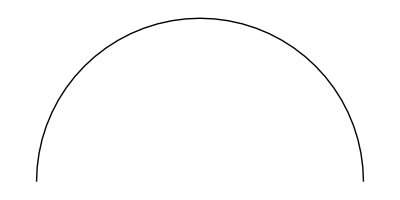

```mathematica
Region[Circle[{0,0},220,{0Degree,180Degree}]]
```

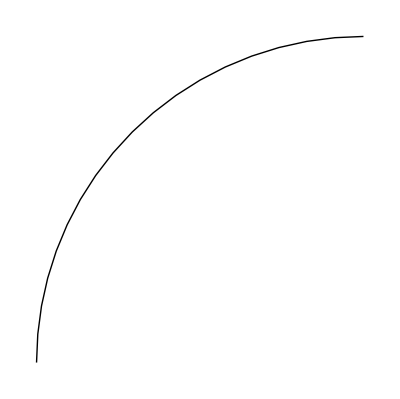

```mathematica
Region[Circle[{0,0},220,{90Degree,180Degree}]]
```

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{0Degree,180Degree}]]]]
```

220 π m

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{90Degree,180Degree}]]]]
```

110 π m

```mathematica
solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==1/2 √(((1/48400 per meter^2) (257217444 km^6/h^4+4 (8019 π km^3/h^2+(0 km^2/h^2) (-110 π m+TraditionalForm`‖PR‖ ArcLength))^2))/(TraditionalForm`‖PR‖ ArcLength)^2)}

```mathematica
solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==1/2 √(((1/48400 per meter^2) (257217444 km^6/h^4+4 (8019 π km^3/h^2+(0 km^2/h^2) (-110 π m+TraditionalForm`‖PR‖ ArcLength))^2))/(TraditionalForm`‖PR‖ ArcLength)^2)}

```mathematica
FullForm[Hold[solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}]]
```

Hold[ReplaceRepeated[solvedEquation,List[Rule[QuantityVariable["r","RadiusOfCurvature"],Quantity[220,"Meters"]],Rule[QuantityVariable[Subscript["v","P"],"Velocity"],Quantity[0,Times["Kilometers",Power["Hours",-1]]]],Rule[QuantityVariable[Subscript["v","R"],"Velocity"],Quantity[270,Times["Kilometers",Power["Hours",-1]]]],Rule[QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"],FullSimplify[RegionMeasure[Region[Circle[List[0,0],Quantity[220,"Meters"],List[Times[90,Degree],Times[180,Degree]]]]]]],Rule[QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"],FullSimplify[RegionMeasure[Region[Circle[List[0,0],Quantity[220,"Meters"],List[0,Times[180,Degree]]]]]]]]]]

```mathematica
solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))}

```mathematica
1/2 √(1/("‖PR‖" "ArcLength")^2)//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

1/2 √(1/(‖PR‖ ArcLength)^2)

```mathematica
FullForm[Hold[1/2 √(1/("‖PR‖" "ArcLength")^2)//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}]]
```

Hold[ReplaceRepeated[Times[Times[1,Power[2,-1]],Sqrt[Times[1,Power[Power[QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"],2],-1]]]],List[Rule[QuantityVariable["r","RadiusOfCurvature"],Quantity[220,"Meters"]],Rule[QuantityVariable[Subscript["v","P"],"Velocity"],Quantity[0,Times["Kilometers",Power["Hours",-1]]]],Rule[QuantityVariable[Subscript["v","R"],"Velocity"],Quantity[270,Times["Kilometers",Power["Hours",-1]]]],Rule[QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"],FullSimplify[RegionMeasure[Region[Circle[List[0,0],Quantity[220,"Meters"],List[Times[90,Degree],Times[180,Degree]]]]]]],Rule[QuantityVariable["TraditionalForm`‖PR\[RightDoubleBracketingBar]","ArcLength"],FullSimplify[RegionMeasure[Region[Circle[List[0,0],Quantity[220,"Meters"],List[0,Times[180,Degree]]]]]]]]]]

```mathematica
//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==1/2 √(((1/48400 per meter^2) (257217444 km^6/h^4+4 (8019 π km^3/h^2+(0 km^2/h^2) (-110 π m+‖PR‖ ArcLength))^2))/(‖PR‖ ArcLength)^2)}

```mathematica
FullForm[Hold[solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}]]
```

Hold[ReplaceRepeated[solvedEquation,List[Rule[QuantityVariable["r","RadiusOfCurvature"],Quantity[220,"Meters"]],Rule[QuantityVariable[Subscript["v","P"],"Velocity"],Quantity[0,Times["Kilometers",Power["Hours",-1]]]],Rule[QuantityVariable[Subscript["v","R"],"Velocity"],Quantity[270,Times["Kilometers",Power["Hours",-1]]]],Rule[QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"],FullSimplify[RegionMeasure[Region[Circle[List[0,0],Quantity[220,"Meters"],List[Times[90,Degree],Times[180,Degree]]]]]]],Rule[QuantityVariable["TraditionalForm`‖PR\[RightDoubleBracketingBar]","ArcLength"],FullSimplify[RegionMeasure[Region[Circle[List[0,0],Quantity[220,"Meters"],List[0,Times[180,Degree]]]]]]]]]]

```mathematica
FullForm[solvedEquation]
```

StandardForm[List[Equal[QuantityVariable["a","Acceleration"],Times[Rational[1,2],Power[Times[Power[QuantityVariable["r","RadiusOfCurvature"],-2],Power[QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"],-2],Plus[Times[Power[QuantityVariable["r","RadiusOfCurvature"],2],Power[Plus[Power[QuantityVariable[Subscript["v","P"],"Velocity"],2],Times[-1,Power[QuantityVariable[Subscript["v","R"],"Velocity"],2]]],2]],Times[4,Power[Plus[Times[Plus[Times[-1,QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"]],QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"]],Power[QuantityVariable[Subscript["v","P"],"Velocity"],2]],Times[QuantityVariable["\[LeftDoubleBracketingBar]PQ\[RightDoubleBracketingBar]","ArcLength"],Power[QuantityVariable[Subscript["v","R"],"Velocity"],2]]],2]]]],Rational[1,2]]]]]]

```mathematica
solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==1/2 √(((1/48400 per meter^2) (257217444 km^6/h^4+4 (8019 π km^3/h^2+(0 km^2/h^2) (-110 π m+‖PR‖ ArcLength))^2))/(‖PR‖ ArcLength)^2)}

```mathematica
solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],QuantityVariable["‖PR‖","ArcLength"]->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==(1250 √(257217444+257217444 π^2))/(121 π) km/h^2}

```mathematica
solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==(1250 √(257217444+257217444 π^2))/(121 π) km/h^2}

```mathematica
QuantityVariable["‖PR‖","ArcLength"]
```

```mathematica
FullForm["\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength"]
```

QuantityVariable["TraditionalForm`‖PR\[RightDoubleBracketingBar]","ArcLength"]

```mathematica
FullForm["\!\(\(TraditionalForm\`‖\)\)PR‖" "ArcLength"]
```

QuantityVariable["TraditionalForm`‖PR\[RightDoubleBracketingBar]","ArcLength"]

```mathematica
FullForm["‖PR‖" "ArcLength"]
```

QuantityVariable["\[LeftDoubleBracketingBar]PR\[RightDoubleBracketingBar]","ArcLength"]

```mathematica
FormulaLookup["ArcLength"]
```

{CircleArcLength}

```mathematica
FormulaData/@FormulaLookup["ArcLength"]
```

{s ArcLength==r Radius θ Angle}

```mathematica
FormulaData["CircleArcLength","QuantityVariableTable"]
```

symbol | description | physical quantity | dimensions
s | arc length | ArcLength | {LengthUnit,1}
r | radius | Radius | {LengthUnit,1}
θ | plane angle | Angle | {AngleUnit,1}

```mathematica
FormulaData["CircleArcLength","Classes"]
```

{Mathematics,{Mathematics,PlaneGeometry}}

```mathematica
FormulaData["CircleArcLength",{"r" "Radius"->Quantity[220, "Meters"],"θ" "Angle"->Quantity[90, "AngularDegrees"]}]
```

s ArcLength==(11 π)/100 km

```mathematica
N[FormulaData["CircleArcLength",{"r" "Radius"->Quantity[220, "Meters"],"θ" "Angle"->Quantity[90, "AngularDegrees"]}]]
```

s ArcLength==0.345575 km

```mathematica
N[FormulaData["CircleArcLength",{"r" "Radius"->Quantity[220, "Meters"],"θ" "Angle"->Quantity[180, "AngularDegrees"]}]]
```

s ArcLength==0.69115 km

```mathematica
UnitConvert[Quantity[1, "AngularDegrees"],"Milliradians"]
```

(50 π)/9 mrad

Maybe if radians are too small to use a solution would be to use milliradians instead. Sometimes it can be easier to use 37 degrees instead of 0.64577 radians, for example, but the angle could be specified as 645.7718 milliradians, instead as 645.7718 mrad.

```mathematica
N[UnitConvert[Quantity[1, "AngularDegrees"],"Milliradians"]]
```

17.4533 mrad

```mathematica
N[UnitConvert[Quantity[37, "AngularDegrees"],"Radians"]]
```

0.645772 rad

```mathematica
N[UnitConvert[Quantity[37, "AngularDegrees"],"Milliradians"]]
```

645.772 mrad

```mathematica
N[UnitConvert[Quantity[645, "Milliradians"],{"AngularDegrees","Radians"}]]
```

{36.9558 °,0.645 rad}

```mathematica
UnitConvert["645"]
```

645 mrad

WolframAlphaQueryResults

```mathematica
UnitDimensions[Quantity[1, "Revolutions"]]
```

{{RevolutionUnit,1}}

```mathematica
UnitConvert[Quantity[1, "Revolutions"],{"Radians","Milliradians","Degrees"}]
```

{$Failed,$Failed,$Failed}

```mathematica
AssociationMap[UnitDimensions][{Quantity[1, "Revolutions"],Quantity[1, "Radians"],Quantity[1, "Milliradians"],Quantity[1, "AngularDegrees"]}]
```

<|1 rev→{{RevolutionUnit,1}},1 rad→{{AngleUnit,1}},1 mrad→{{AngleUnit,1}},1 °→{{AngleUnit,1}}|>

```mathematica
Quantity[""]
```

```mathematica
?CompatibleUnitQ
```

```mathematica
Select[CompatibleUnitQ[#,"AngularDegrees"]&][{Quantity[1, "Revolutions"],Quantity[1, "Radians"],Quantity[1, "Milliradians"],Quantity[1, "AngularDegrees"]}]
```

{1 rad,1 mrad,1 °}

convert 5 mrad to revolutions

WolframAlphaQueryResults

```mathematica
WolframAlpha["convert 5 mrad to revolutions",{{"Result",1},"QuantityData"}]
```

1/(400 π) rev

```mathematica
UnitConvert[Quantity[1/(400 π),"Revolutions"],"radians"]
```

$Failed

```mathematica
WolframAlpha["convert 5 mrad to revolutions",{{"Result",1},"ComputableData"}]
```

1/(400 π) rev

```mathematica
FullForm[WolframAlpha["convert 5 mrad to revolutions",{{"Result",1},"ComputableData"}]]
```

Quantity[Times[Rational[1,400],Power[Pi,-1]],"Revolutions"]

```mathematica
WolframAlpha["convert 5 mrad to revolutions",IncludePods->"Result",AppearanceElements->{"Pods"},TimeConstraint->{20,Automatic,Automatic,Automatic}]
```

WolframAlphaQueryResults

```mathematica
UnitConvert[Quantity["Radians"],"Revolutions"/Pi]
```

UnitConvert[1 rad,Revolutions/π]

```mathematica
CompatibleUnitQ[Quantity[1/(400 π), "Revolutions"],Quantity["Radians"]]
```

False

```mathematica
CompatibleUnitQ[Quantity["Rotations"],Quantity["Radians"]]
```

False

```mathematica
AssociationMap[FormulaData][FormulaLookup["Arc"]]
```

<|ArchimedesNumber→Ar ArchimedesNumber==(g GravitationalAcceleration (l Length)^3 (ρ MassDensity-ρ_0 MassDensity) ρ_0 MassDensity)/(η DynamicViscosity)^2,CircleArcLength→s ArcLength==r Radius θ Angle,CircularCoilMaximalMagneticInduction→B MagneticFluxDensity==(Log[(2 R Radius+r Radius √(((l Length)^2+4 (R Radius)^2)/(r Radius)^2))/((2+√(4+(l Length)^2/(r Radius)^2)) r Radius)] (1/2 μ_0) I ElectricCurrent N MultiplicativeConstants)/(-r Radius+R Radius),SingleLayerCircularCoilSelfInductance→L MagneticInductance==((1/3 μ_0) (N MultiplicativeConstants)^2 (r Radius)^2 (-(8 r Radius)/(l Length)+((l Length)^2 √(1+(4 (r Radius)^2)/(l Length)^2) (EllipticK[(4 (r Radius)^2)/((l Length)^2 (1+(4 (r Radius)^2)/(l Length)^2))]+EllipticE[(4 (r Radius)^2)/((l Length)^2 (1+(4 (r Radius)^2)/(l Length)^2))] (-1+(4 (r Radius)^2)/(l Length)^2)))/(r Radius)^2))/(l Length),SingleLayerCircularCoilSmallRadiusSelfInductance→L MagneticInductance==((π μ_0) (N MultiplicativeConstants)^2 (r Radius)^2)/(l Length),SingleLayerRectangularCoilSelfInductance→L MagneticInductance==1/(l Length)^2(1/(3 π) μ_0) (-(a Length)^3-(b Length)^3+3 π a Length b Length l Length-3 (ArcSinh[(b Length)/(a Length)] (a Length)^2 b Length-ArcSinh[(b Length)/(√((a Length)^2+(l Length)^2))] (a Length)^2 b Length+ArcSinh[(a Length)/(b Length)] a Length (b Length)^2-ArcSinh[(a Length)/(√((b Length)^2+(l Length)^2))] a Length (b Length)^2+2 ArcTan[(a Length b Length)/(l Length √((a Length)^2+(b Length)^2+(l Length)^2))] a Length b Length l Length-ArcSinh[(a Length)/(l Length)] a Length (l Length)^2+ArcSinh[(a Length)/(√((b Length)^2+(l Length)^2))] a Length (l Length)^2-ArcSinh[(b Length)/(l Length)] b Length (l Length)^2+ArcSinh[(b Length)/(√((a Length)^2+(l Length)^2))] b Length (l Length)^2)+(a Length)^2 (√((a Length)^2+(b Length)^2)+√((a Length)^2+(l Length)^2)-√((a Length)^2+(b Length)^2+(l Length)^2))+(b Length)^2 (√((a Length)^2+(b Length)^2)+√((b Length)^2+(l Length)^2)-√((a Length)^2+(b Length)^2+(l Length)^2))+2 (l Length)^2 (l Length-√((a Length)^2+(l Length)^2)-√((b Length)^2+(l Length)^2)+√((a Length)^2+(b Length)^2+(l Length)^2))) (N MultiplicativeConstants)^2,{CircleSectorArea,ArcLength}→A Area==(R Radius s ArcLength)/2,{CircularCurrentLoop,Distance}→B MagneticFluxDensity==((1/2 μ_0) I ElectricCurrent (R Radius)^2)/(((d Distance)^2+(R Radius)^2)^(3/2)),{CircularCurrentLoop,Loops}→B MagneticFluxDensity==((1/2 μ_0) I ElectricCurrent N MultiplicativeConstants)/(R Radius),{CircularCurrentLoop,Standard}→B MagneticFluxDensity==((1/2 μ_0) I ElectricCurrent)/(R Radius),{ColebrookWhiteEquation,DarcyFrictionFactor}→1/(√(f_D DarcyFrictionFactor))==-(2 Log[0.27027 K MultiplicativeConstants+2.51/(Re ReynoldsNumber √(f_D DarcyFrictionFactor))])/Log[10],{DarcysLaw,HydraulicGradient}→Q VolumeFlowRate==A Area i MultiplicativeConstants K Speed,{DarcysLaw,PressureDifference}→Q VolumeFlowRate==-(A Area ΔP Pressure κ HydraulicPermeability)/(L Length η DynamicViscosity),{BondPriceBetweenCoupons,CleanPrice,RegularCoupon}→P_c Money==-(DCS MultiplicativeConstants i MultiplicativeConstants par Money)/(2 DIC MultiplicativeConstants)+(2^(-(DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)+n MultiplicativeConstants) par Money (2+y MultiplicativeConstants)^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (y MultiplicativeConstants+i MultiplicativeConstants (-1+2^(-n MultiplicativeConstants) (2+y MultiplicativeConstants)^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,DirtyPrice,RegularCoupon}→P_d Money==(2^(-(DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)+n MultiplicativeConstants) par Money (2+y MultiplicativeConstants)^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (y MultiplicativeConstants+i MultiplicativeConstants (-1+2^(-n MultiplicativeConstants) (2+y MultiplicativeConstants)^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{CircularCurrentLoop,Loops,Distance}→B MagneticFluxDensity==((1/2 μ_0) I ElectricCurrent N MultiplicativeConstants (R Radius)^2)/(((d Distance)^2+(R Radius)^2)^(3/2)),{BondPriceBetweenCoupons,CleanPrice,RegularCoupon,CouponFrequency}→P_c Money==-(DCS MultiplicativeConstants i MultiplicativeConstants par Money)/(DIC MultiplicativeConstants f MultiplicativeConstants)+(par Money ((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (y MultiplicativeConstants+i MultiplicativeConstants (-1+((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,CleanPrice,RegularCoupon,DayCountConvention}→P_c Money==-(DCS MultiplicativeConstants i MultiplicativeConstants par Money)/(2 DIC MultiplicativeConstants)+(2^(-(DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)+n MultiplicativeConstants) par Money (2+y MultiplicativeConstants)^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (y MultiplicativeConstants+i MultiplicativeConstants (-1+2^(-n MultiplicativeConstants) (2+y MultiplicativeConstants)^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,CleanPrice,RegularCoupon,RedemptionValue}→P_c Money==-(DCS MultiplicativeConstants i MultiplicativeConstants par Money)/(2 DIC MultiplicativeConstants)+(2^(-(DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)+n MultiplicativeConstants) (2+y MultiplicativeConstants)^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (red Money y MultiplicativeConstants+i MultiplicativeConstants par Money (-1+2^(-n MultiplicativeConstants) (2+y MultiplicativeConstants)^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,DirtyPrice,RegularCoupon,CouponFrequency}→P_d Money==(par Money ((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (y MultiplicativeConstants+i MultiplicativeConstants (-1+((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,DirtyPrice,RegularCoupon,DayCountConvention}→P_d Money==(2^(-(DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)+n MultiplicativeConstants) par Money (2+y MultiplicativeConstants)^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (y MultiplicativeConstants+i MultiplicativeConstants (-1+2^(-n MultiplicativeConstants) (2+y MultiplicativeConstants)^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,DirtyPrice,RegularCoupon,RedemptionValue}→P_d Money==(2^(-(DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)+n MultiplicativeConstants) (2+y MultiplicativeConstants)^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (red Money y MultiplicativeConstants+i MultiplicativeConstants par Money (-1+2^(-n MultiplicativeConstants) (2+y MultiplicativeConstants)^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,CleanPrice,RegularCoupon,CouponFrequency,RedemptionValue}→P_c Money==-(DCS MultiplicativeConstants i MultiplicativeConstants par Money)/(DIC MultiplicativeConstants f MultiplicativeConstants)+(((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (red Money y MultiplicativeConstants+i MultiplicativeConstants par Money (-1+((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,CleanPrice,RegularCoupon,DayCountConvention,CouponFrequency}→P_c Money==-(DCS MultiplicativeConstants i MultiplicativeConstants par Money)/(DIC MultiplicativeConstants f MultiplicativeConstants)+(par Money ((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (y MultiplicativeConstants+i MultiplicativeConstants (-1+((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,CleanPrice,RegularCoupon,DayCountConvention,RedemptionValue}→P_c Money==-(DCS MultiplicativeConstants i MultiplicativeConstants par Money)/(2 DIC MultiplicativeConstants)+(2^(-(DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)+n MultiplicativeConstants) (2+y MultiplicativeConstants)^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (red Money y MultiplicativeConstants+i MultiplicativeConstants par Money (-1+2^(-n MultiplicativeConstants) (2+y MultiplicativeConstants)^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,DirtyPrice,RegularCoupon,CouponFrequency,RedemptionValue}→P_d Money==(((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (red Money y MultiplicativeConstants+i MultiplicativeConstants par Money (-1+((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,DirtyPrice,RegularCoupon,DayCountConvention,CouponFrequency}→P_d Money==(par Money ((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (y MultiplicativeConstants+i MultiplicativeConstants (-1+((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,DirtyPrice,RegularCoupon,DayCountConvention,RedemptionValue}→P_d Money==(2^(-(DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)+n MultiplicativeConstants) (2+y MultiplicativeConstants)^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (red Money y MultiplicativeConstants+i MultiplicativeConstants par Money (-1+2^(-n MultiplicativeConstants) (2+y MultiplicativeConstants)^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,CleanPrice,RegularCoupon,DayCountConvention,CouponFrequency,RedemptionValue}→P_c Money==-(DCS MultiplicativeConstants i MultiplicativeConstants par Money)/(DIC MultiplicativeConstants f MultiplicativeConstants)+(((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (red Money y MultiplicativeConstants+i MultiplicativeConstants par Money (-1+((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^(n MultiplicativeConstants))))/(y MultiplicativeConstants),{BondPriceBetweenCoupons,DirtyPrice,RegularCoupon,DayCountConvention,CouponFrequency,RedemptionValue}→P_d Money==(((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^((DCS MultiplicativeConstants)/(DIC MultiplicativeConstants)-n MultiplicativeConstants) (red Money y MultiplicativeConstants+i MultiplicativeConstants par Money (-1+((f MultiplicativeConstants+y MultiplicativeConstants)/(f MultiplicativeConstants))^(n MultiplicativeConstants))))/(y MultiplicativeConstants)|>

```mathematica
AssociationMap[FormulaData][FormulaLookup["Angular"]]
```

<|AngularDiameter→δ Angle==2 ArcTan[(d Diameter)/(2 D Distance)],ErlangB→P_b MultiplicativeConstants==(ⅇ^(-E TelecommunicationsTraffic) (E TelecommunicationsTraffic)^(m MultiplicativeConstants))/Gamma[1+m MultiplicativeConstants,E TelecommunicationsTraffic],ErlangC→P_w MultiplicativeConstants==(E TelecommunicationsTraffic)^(m MultiplicativeConstants)/((E TelecommunicationsTraffic)^(m MultiplicativeConstants)-ⅇ^(E TelecommunicationsTraffic) Gamma[m MultiplicativeConstants,E TelecommunicationsTraffic] (E TelecommunicationsTraffic-m MultiplicativeConstants)),AngularFrequency→ν Frequency==(ω AngularFrequency)/(2 π),HohmannAngularAlignment→α Angle==π (1-(√((1+(r_1 Length)/(r_2 Length))^3))/(2 √2)),RigidBodyAngularMomentum→{L AngularMomentum==I MomentOfInertia ω AngularVelocity,ω AngularVelocity==(2 π rad/rev) n RevolutionRate},SingleLayerRectangularCoilSelfInductance→L MagneticInductance==1/(l Length)^2(1/(3 π) μ_0) (-(a Length)^3-(b Length)^3+3 π a Length b Length l Length-3 (ArcSinh[(b Length)/(a Length)] (a Length)^2 b Length-ArcSinh[(b Length)/(√((a Length)^2+(l Length)^2))] (a Length)^2 b Length+ArcSinh[(a Length)/(b Length)] a Length (b Length)^2-ArcSinh[(a Length)/(√((b Length)^2+(l Length)^2))] a Length (b Length)^2+2 ArcTan[(a Length b Length)/(l Length √((a Length)^2+(b Length)^2+(l Length)^2))] a Length b Length l Length-ArcSinh[(a Length)/(l Length)] a Length (l Length)^2+ArcSinh[(a Length)/(√((b Length)^2+(l Length)^2))] a Length (l Length)^2-ArcSinh[(b Length)/(l Length)] b Length (l Length)^2+ArcSinh[(b Length)/(√((a Length)^2+(l Length)^2))] b Length (l Length)^2)+(a Length)^2 (√((a Length)^2+(b Length)^2)+√((a Length)^2+(l Length)^2)-√((a Length)^2+(b Length)^2+(l Length)^2))+(b Length)^2 (√((a Length)^2+(b Length)^2)+√((b Length)^2+(l Length)^2)-√((a Length)^2+(b Length)^2+(l Length)^2))+2 (l Length)^2 (l Length-√((a Length)^2+(l Length)^2)-√((b Length)^2+(l Length)^2)+√((a Length)^2+(b Length)^2+(l Length)^2))) (N MultiplicativeConstants)^2,TriangularPlateMomentOfInertia→I_z MomentOfInertia==1/36 ((a Length)^2+(b Length)^2+(c Length)^2) m Mass,{AverageAngularVelocity,Angles}→ω̄ AngularVelocity==(θ_f Angle-θ_i Angle)/(t Time),{AverageAngularVelocity,AngularDisplacement}→ω̄ AngularVelocity==(θ Angle)/(t Time),{AverageAngularVelocity,Velocities}→1/2 (ω_f AngularVelocity+ω_i AngularVelocity)==(θ Angle)/(t Time),{BlackHoleEntropy,AngularMomentum}→S Entropy==(π k c^3/(G ℏ)) (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))^2),{BlackHoleEventHorizonArea,AngularMomentum}→A Area==4 π (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))^2),{BlackHoleEventHorizonRadius,AngularMomentum}→r Radius==( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2),{BlackHoleSurfaceGravity,AngularMomentum}→k GravitationalAcceleration==(( c^2) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))),{BlackHoleTemperature,AngularMomentum}→T Temperature==((1/(2 π) ℏ c/k) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))/((-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2+(2 G/c^2) M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))),{CapacitiveReactance,AngularFrequency}→X_C ElectricReactance==1/(C ElectricCapacitance ω AngularFrequency),{CentripetalAcceleration,AngularVelocity}→a Acceleration==r Radius (ω AngularVelocity)^2,{CentripetalForce,AngularVelocity}→F Force==(1 per radian^2) m Mass r Radius (ω AngularVelocity)^2,{DistanceSpeedTimeCircularForm,AngularAcceleration}→θ Angle==1/2 (t Time)^2 α AngularAcceleration,{ElectromagneticSkinDepth,AngularFrequency}→δ Depth==(√2 √(1/(ϵ ElectricPermittivity μ MagneticPermeability)))/(√(-1+√(1+(σ ElectricConductivity)^2/((ϵ ElectricPermittivity)^2 (ω AngularFrequency)^2))) ω AngularFrequency),{PhotonEnergy,AngularFrequency}→E Energy==( ℏ) ω AngularFrequency,{SpeedAccelerationDistanceCircularForm,AngularDisplacement}→(ω_f AngularVelocity)^2==2 α AngularAcceleration θ Angle+(ω_i AngularVelocity)^2,{SpeedAccelerationTimeCircularForm,InitialAngularSpeed}→ω_f AngularVelocity==t Time α AngularAcceleration+ω_i AngularVelocity,{SpeedAccelerationTimeCircularForm,NoInitialAngularSpeed}→ω AngularVelocity==t Time α AngularAcceleration,{WaveSpeed,AngularFrequency}→v Speed==(λ Wavelength ω AngularFrequency)/(2 π),{AngularToLinearVelocity,AngularVelocity,Diameter}→v LinearSpeed==(d Diameter ω AngularVelocity)/2,{AngularToLinearVelocity,AngularVelocity,OrbitDistance}→v LinearSpeed==ω AngularVelocity d_o Distance,{AngularToLinearVelocity,AngularVelocity,Radius}→v LinearSpeed==r Radius ω AngularVelocity,{AngularToLinearVelocity,Period,Diameter}→v LinearSpeed==(π d Diameter)/(T Period),{AngularToLinearVelocity,Period,OrbitDistance}→v LinearSpeed==(2 π d_o Distance)/(T Period),{AngularToLinearVelocity,Period,Radius}→v LinearSpeed==(2 π r Radius)/(T Period),{AngularToLinearVelocity,RotationRate,Diameter}→v LinearSpeed==(π /rev) d Diameter n RevolutionRate,{AngularToLinearVelocity,RotationRate,OrbitDistance}→v LinearSpeed==(2 π /rev) n RevolutionRate d_o Distance,{AngularToLinearVelocity,RotationRate,Radius}→v LinearSpeed==(2 π /rev) n RevolutionRate r Radius,{AverageAngularVelocity,Velocities,Angles}→1/2 (ω_f AngularVelocity+ω_i AngularVelocity)==(θ_f Angle-θ_i Angle)/(t Time),{BlackHoleEntropy,Charge,AngularMomentum}→S Entropy==(π k c^3/(G ℏ)) (((1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+(( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))^2),{BlackHoleEventHorizonArea,Charge,AngularMomentum}→A Area==4 π (( G/c^2) M Mass+√(( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2))^2,{BlackHoleEventHorizonRadius,Charge,AngularMomentum}→r Radius==( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2+(-1/(4 π) G/(ε_0 c^4)) (Q ElectricCharge)^2),{BlackHoleSurfaceGravity,Charge,AngularMomentum}→k GravitationalAcceleration==((1/2 c^4/G) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))/(M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))),{BlackHoleTemperature,Charge,AngularMomentum}→T Temperature==((1/(4 π) ℏ c^3/(k G)) √(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))/(M Mass (( G/c^2) M Mass+√(((-1 /c^2) (J AngularMomentum)^2)/(M Mass)^2+( G^2/c^4) (M Mass)^2))),{CentripetalAcceleration,AngularVelocity,Diameter}→a Acceleration==1/2 d Diameter (ω AngularVelocity)^2,{CentripetalAcceleration,AngularVelocity,OrbitDistance}→a Acceleration==(ω AngularVelocity)^2 d_o Distance,{DeBroglieRelations,AngularFrequency,KineticEnergy}→ω AngularFrequency==(1 /ℏ) K Energy,{DeBroglieRelations,AngularFrequency,Momentum}→ω AngularFrequency==((1/2 /ℏ) (p Momentum)^2)/(m Mass),{DeBroglieRelations,AngularFrequency,Velocity}→ω AngularFrequency==(1/2 /ℏ) m Mass (v Speed)^2,{DeBroglieRelationsRelativistic,AngularFrequency,KineticEnergy}→ω AngularFrequency==(1 /ℏ) K Energy,{DeBroglieRelationsRelativistic,AngularFrequency,Momentum}→ω AngularFrequency==(1 /ℏ) ((-1 c^2) m Mass+√(( c^4) (m Mass)^2+( c^2) (p Momentum)^2)),{DeBroglieRelationsRelativistic,AngularFrequency,Velocity}→ω AngularFrequency==(( c^2/ℏ) m Mass)/(√(1+(-1 /c^2) (v Speed)^2)),{DistanceSpeedTimeCircularForm,InitialAngle,AngularAcceleration}→θ_f Angle==1/2 (t Time)^2 α AngularAcceleration+θ_i Angle,{DistanceSpeedTimeCircularForm,InitialAngularSpeed,AngularAcceleration}→θ Angle==1/2 (t Time)^2 α AngularAcceleration+t Time ω_i AngularVelocity,{Torque,AngularAcceleration,MomentOfInertia}→τ Torque==I MomentOfInertia α AngularAcceleration,{WaveGuideRectangular,Frequency,TransverseElectric}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),η ElectricResistance==( √μ_0/√ε_0) √(1-(f_c Frequency)^2/(f Frequency)^2)},{WaveGuideRectangular,Frequency,TransverseMagnetic}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangular,Wavelength,TransverseElectric}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangular,Wavelength,TransverseMagnetic}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),η ElectricResistance==( √μ_0/√ε_0) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2)},{DistanceSpeedTimeCircularForm,InitialAngle,InitialAngularSpeed,AngularAcceleration}→θ_f Angle==1/2 (t Time)^2 α AngularAcceleration+θ_i Angle+t Time ω_i AngularVelocity,{WaveGuideRectangularAttenuation,Frequency,Conductivity,TransverseElectric}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√((π μ_0) f Frequency σ_c ElectricConductivity)),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) (((1+(b Length)/(a Length)) (f_c Frequency)^2)/(f Frequency)^2+(((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(f_c Frequency)^2/(f Frequency)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)) R_s ElectricResistance)/(b Length √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Frequency,Conductivity,TransverseMagnetic}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==1/(√((π μ_0) f Frequency σ_c ElectricConductivity)),η ElectricResistance==( √μ_0/√ε_0) √(1-(f_c Frequency)^2/(f Frequency)^2),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Frequency,Resistivity,TransverseElectric}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√(((1/π /μ_0) ρ_c ElectricResistivity)/(f Frequency)),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) (((1+(b Length)/(a Length)) (f_c Frequency)^2)/(f Frequency)^2+(((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(f_c Frequency)^2/(f Frequency)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)) R_s ElectricResistance)/(b Length √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Frequency,Resistivity,TransverseMagnetic}→{f_c Frequency==(1/2 c) √((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2),ν̃ Wavenumber==(2 π /c) √((f Frequency)^2-(f_c Frequency)^2),v Velocity==c/(√(1-(f_c Frequency)^2/(f Frequency)^2)),v_g Velocity==( c) √(1-(f_c Frequency)^2/(f Frequency)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(f_c Frequency)^2/(f Frequency)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√(((1/π /μ_0) ρ_c ElectricResistivity)/(f Frequency)),η ElectricResistance==( √μ_0/√ε_0) √(1-(f_c Frequency)^2/(f Frequency)^2),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(f_c Frequency)^2/(f Frequency)^2))},{WaveGuideRectangularAttenuation,Wavelength,Conductivity,TransverseElectric}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==√(((1/π /(μ_0 c)) λ Wavelength)/(σ_c ElectricConductivity)),η ElectricResistance==( √μ_0/√ε_0) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_c Wavenumber==((2 √ε_0/√μ_0) R_s ElectricResistance ((((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(λ Wavelength)^2/(λ_c Wavelength)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)+((1+(b Length)/(a Length)) (λ Wavelength)^2)/(λ_c Wavelength)^2))/(b Length √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangularAttenuation,Wavelength,Conductivity,TransverseMagnetic}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==((1/2 √μ_0/√ε_0) σ_d ElectricConductivity)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),R_s ElectricResistance==1/(δ Depth σ_c ElectricConductivity),δ Depth==√(((1/π /(μ_0 c)) λ Wavelength)/(σ_c ElectricConductivity)),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangularAttenuation,Wavelength,Resistivity,TransverseElectric}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√((1/π /(μ_0 c)) λ Wavelength ρ_c ElectricResistivity),η ElectricResistance==( √μ_0/√ε_0) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_c Wavenumber==((2 √ε_0/√μ_0) R_s ElectricResistance ((((b Length)^2 (m MultiplicativeConstants)^2+a Length b Length (n MultiplicativeConstants)^2) (1-(λ Wavelength)^2/(λ_c Wavelength)^2))/((b Length)^2 (m MultiplicativeConstants)^2+(a Length)^2 (n MultiplicativeConstants)^2)+((1+(b Length)/(a Length)) (λ Wavelength)^2)/(λ_c Wavelength)^2))/(b Length √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))},{WaveGuideRectangularAttenuation,Wavelength,Resistivity,TransverseMagnetic}→{λ_c Wavelength==2/(√((m MultiplicativeConstants)^2/(a Length)^2+(n MultiplicativeConstants)^2/(b Length)^2)),ν̃ Wavenumber==√((2 π)/(λ Wavelength)^2-(2 π)/(λ_c Wavelength)^2),v Velocity==c/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),v_g Velocity==( c) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2),α_d Wavenumber==(1/2 √μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2) ρ_d ElectricResistivity),R_s ElectricResistance==(ρ_c ElectricResistivity)/(δ Depth),δ Depth==√((1/π /(μ_0 c)) λ Wavelength ρ_c ElectricResistivity),η ElectricResistance==(√μ_0/√ε_0)/(√(1-(λ Wavelength)^2/(λ_c Wavelength)^2)),α_c Wavenumber==((2 √ε_0/√μ_0) ((b Length)^3 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) R_s ElectricResistance)/(b Length (a Length (b Length)^2 (m MultiplicativeConstants)^2+(a Length)^3 (n MultiplicativeConstants)^2) √(1-(λ Wavelength)^2/(λ_c Wavelength)^2))}|>

```mathematica
180/Degree
```

180/°

```mathematica
N[180/Degree]
```

10313.2

```mathematica
N[180Degree]
```

3.14159

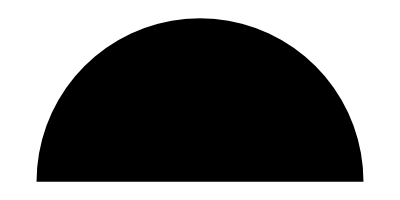

```mathematica
Graphics[Disk[{0,0},1,{180Degree,0}]]
```

```mathematica
DiscretizeGraphics[Graphics[Disk[{0,0},1,{180Degree,0}]]]
```

EmptyRegion[2]

```mathematica
Region[Disk[{0,0},1,{180Degree,0}]]
```

-Graphics-

```mathematica
Region[Circle[{0,0},1,{180Degree,0}]]
```

-Graphics-

```mathematica
RegionMeasure[Region[Circle[{0,0},1,{180Degree,0}]]]
```

180 °

```mathematica
N[RegionMeasure[Region[Circle[{0,0},1,{180Degree,0}]]]]
```

3.14159

```mathematica
N[RegionMeasure[Region[Circle[{0,0},220,{180Degree,0}]]]]
```

691.15

```mathematica
RegionMeasure[Region[Circle[{0,0},220,{180Degree,0}]]]
```

39600 °

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},220,{180Degree,0}]]]]
```

220 π

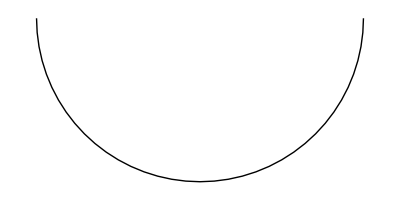

```mathematica
Region[Circle[{0,0},220,{-180Degree,0}]]
```

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},220,{-180Degree,0}]]]]
```

220 π

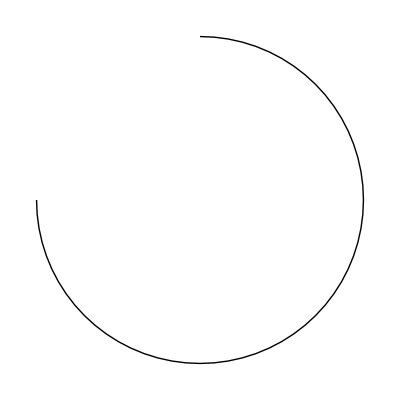

```mathematica
Region[Circle[{0,0},220,{-180Degree,90Degree}]]
```

```mathematica
Region[Circle[{0,0},220,{90Degree,180Degree}]]
```

-Graphics-

```mathematica
Region[Circle[{0,0},Quantity[220,"Meters"],{90Degree,180Degree}]]
```

Region[…]

```mathematica
RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{90Degree,180Degree}]]]
```

19800 ° m

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{90Degree,180Degree}]]]]
```

110 π m

```mathematica
RegionMeasure[Region[Circle[{0,0},220,{90Degree,180Degree}]]]
```

19800 °

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},220,{90Degree,180Degree}]]]]
```

110 π

```mathematica
Quantity[FullSimplify[RegionMeasure[Region[Circle[{0,0},220,{90Degree,180Degree}]]]],"Meters"]
```

110 π m

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},220,{-180Degree,90Degree}]]]]
```

330 π

### 25*(II) A car at the Indianapolis 500 accelerates uniformly from the pit area, going from rest to 270 km/h in a semicircular arc with a radius of 220 m. Determine the tangential and radial acceleration of the car when it is halfway through the arc, assuming constant tangential acceleration. If the curve were flat, what coefficient of static friction would be necessary between the tires and the road to provide this acceleration with no slipping or skidding?

#### Redoing the problem again:

```mathematica
FIRSTKINEMATICSEQUATION=(Subscript["v", "R"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PR‖" "ArcLength")
```

(v_R Velocity)^2==2 ‖PR‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
SECONDKINEMATICSEQUATION=(Subscript["v", "Q"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PQ‖" "ArcLength")
```

(v_Q Velocity)^2==2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
CENTRIPETALACCELERATION=Subscript["a", "c"] "CentripetalAcceleration"==(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")
```

a_c CentripetalAcceleration==(v_Q Velocity)^2/(r RadiusOfCurvature)

```mathematica
NONUNIFORMCIRCULARMOTIONEQUATION="a" "Acceleration"==√((Subscript["a", "c"] "CentripetalAcceleration")^2+(Subscript["a", "tan"] "TangentialAcceleration")^2)
```

a Acceleration==√((a_c CentripetalAcceleration)^2+(a_tan TangentialAcceleration)^2)

Solve the system of equations:

```mathematica
Reap[MapAt[FullSimplify,NONUNIFORMCIRCULARMOTIONEQUATION//.Join[Sow[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"],"solution to solving the first kinematics equation for a_tan"],Sow[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",,Assumptions->{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],"solution to solving the second kinematics equation for v_Q"],Sow[Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"],"centripetal acceleration"],2],{1,2}],_,Rule]
```

{{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))},{solution to solving the first kinematics equation for a_tan→{{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}}},solution to solving the second kinematics equation for v_Q→{{{v_Q Velocity→√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2)}}},centripetal acceleration→{{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}}}}

```mathematica
MapAt[Association,,2]
```

{{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))},<|solution to solving the first kinematics equation for a_tan→{{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}}},solution to solving the second kinematics equation for v_Q→{{{v_Q Velocity→√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2)}}},centripetal acceleration→{{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}}|>}

```mathematica
solvedEquation=MapAt[FullSimplify,NONUNIFORMCIRCULARMOTIONEQUATION//.Join[Sow[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"],"solution to solving the first kinematics equation for a_tan"],Sow[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",,Assumptions->{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],"solution to solving the second kinematics equation for v_Q"],Sow[Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"],"centripetal acceleration"],2],{1,2}]
```

{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))}

The semicircle:

```mathematica
Region[Circle[{0,0},220,{0Degree,180Degree}]]
```

-Graphics-

Halfway through the circle:

```mathematica
Region[Circle[{0,0},220,{90Degree,180Degree}]]
```

-Graphics-

The arc length of the semicircle:

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{0Degree,180Degree}]]]]
```

220 π m

The arc length of half of the semicircle:

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{90Degree,180Degree}]]]]
```

110 π m

The solved equation:

```mathematica
solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==(1250 √(257217444+257217444 π^2))/(121 π) km/h^2}

```mathematica
MapCases[UnitConvert[#,"SIBase"]&,solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]},x_?QuantityQ,All]
```

{a Acceleration==(125 √(257217444+257217444 π^2))/(156816 π) m/s^2}

```mathematica
N[solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}]
```

{a Acceleration==173873. km/h^2}

```mathematica
MapCases[UnitConvert[#,"SIBase"]&,N[solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}],x_?QuantityQ,All]
```

{a Acceleration==13.4161 m/s^2}

```mathematica
Solve[solvedEquation,"a" "Acceleration"]
```

{{a Acceleration→1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))}}

Solve

```mathematica
FrictionEquation="m" "Mass"("g" "GravitationalAcceleration")("μ" "StaticFrictionCoefficient")-"m" "Mass" "a" "Acceleration"==0;
```

```mathematica
Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]
```

{{μ StaticFrictionCoefficient→(a Acceleration)/(g GravitationalAcceleration)}}

```mathematica
Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]//.Solve[solvedEquation,"a" "Acceleration"]
```

{{{μ StaticFrictionCoefficient→(√(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2)))/(2 g GravitationalAcceleration)}}}

```mathematica
Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]//.Solve[solvedEquation,"a" "Acceleration"]//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"g" "GravitationalAcceleration"->Quantity[, "StandardAccelerationOfGravity"]}
```

{{{μ StaticFrictionCoefficient→(156250 √(257217444+257217444 π^2))/(1922299533 π)}}}

```mathematica
N[Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]//.Solve[solvedEquation,"a" "Acceleration"]//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"g" "GravitationalAcceleration"->Quantity[, "StandardAccelerationOfGravity"]}]
```

{{{μ StaticFrictionCoefficient→1.36806}}}

```mathematica
Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]//.Solve[solvedEquation,"a" "Acceleration"]//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"g" "GravitationalAcceleration"->GeogravityModelData["Magnitude"](*my local acceleration of g, not the global average*)}
```

{{{μ StaticFrictionCoefficient→1.36906}}}

```mathematica
Solve[FrictionEquation/.First[(solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}),"μ" "StaticFrictionCoefficient"]
```

Solve[-a Acceleration m Mass+g GravitationalAcceleration m Mass μ StaticFrictionCoefficient==0/.{a Acceleration==(1250 √(257217444+257217444 π^2))/(121 π) km/h^2},μ StaticFrictionCoefficient]

```mathematica
SolvedStaticFrictionEquation=
```

### angles with mrad

645 mrad

WolframAlphaQueryResults

### 25*(II) A car at the Indianapolis 500 accelerates uniformly from the pit area, going from rest to 270 km/h in a semicircular arc with a radius of 220 m. Determine the tangential and radial acceleration of the car when it is halfway through the arc, assuming constant tangential acceleration. If the curve were flat, what coefficient of static friction would be necessary between the tires and the road to provide this acceleration with no slipping or skidding?

Here is a picture with the points labeled. Click on the points to see their names. The name of an arc of a circle is the name of the starting and ending points. For example an arc could be named PQ if it went from point P to point Q. The length of the arc is denoted by ‖PQ‖ in this case. Below this, there is a graphic that displays a tooltip with the name of a point when you hover over it instead of opening up a popup window.

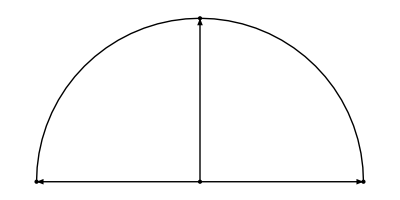

```mathematica
Graphics[{Circle[{0,0},220,{0 Degree,180 Degree}],PopupWindow[Point[{0,220}],Q,],PopupWindow[Point[{-220,0}],P,],PopupWindow[Point[{220,0}],R,],PopupWindow[Point[{0,0}],Center,],PopupWindow[Arrow[{{0,0},{220,0}}],radius=Quantity[220, "Meters"],],PopupWindow[Arrow[{{0,0},{-220,0}}],radius=Quantity[220, "Meters"],],PopupWindow[Arrow[{{0,0},{0,220}}],radius=Quantity[220, "Meters"],]}]
```

```mathematica
Graphics[{Circle[{0,0},220,{0 Degree,180 Degree}],Tooltip[Point[{0,220}],Q],Tooltip[Point[{-220,0}],P],Tooltip[Point[{220,0}],R],Tooltip[Point[{0,0}],Center],Tooltip[Arrow[{{0,0},{220,0}}],radius=Quantity[220, "Meters"]],Tooltip[Arrow[{{0,0},{-220,0}}],radius=Quantity[220, "Meters"]],Tooltip[Arrow[{{0,0},{0,220}}],radius=Quantity[220, "Meters"]]}]
```

-Graphics-

Here is a diagram of the path of the racecar, a semicircle:

```mathematica
Region[Circle[{0,0},220,{0Degree,180Degree}]]
```

-Graphics-

Determine the tangential and radial acceleration of the car when it is halfway through the arc, assuming constant tangential acceleration. This is the picture of the path of the racecar halfway through the arc:

```mathematica
Region[Circle[{0, 0}, 220, {90 Degree,180 Degree}]]
```

-Graphics-

Now we can determine ‖PQ‖ and ‖PR‖.

The semicircle:

```mathematica
Region[Circle[{0,0},220,{0Degree,180Degree}]]
```

-Graphics-

Halfway through the circle:

```mathematica
Region[Circle[{0,0},220,{90Degree,180Degree}]]
```

-Graphics-

The arc length of the semicircle:

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{0Degree,180Degree}]]]]
```

220 π m

The arc length of half of the semicircle:

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{90Degree,180Degree}]]]]
```

110 π m

Our known quantities are the arc length of the arc PR as ‖PR‖ and the velocity at point P as  v_P and the velocity at point R as v_R. This is the kinematic equation we need to solve for the tangential acceleration. The tangential acceleration is constant throughout the time the racecar driver moves, so we don't need to solve for it separately at point Q after we solved for it at point R, for example.

```mathematica
FIRSTKINEMATICSEQUATION=(Subscript["v", "R"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PR‖" "ArcLength")
```

(v_R Velocity)^2==2 ‖PR‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

We'll use this solution later:

```mathematica
Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"]
```

{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}}

We have now determined a_tan. We now need the velocity halfway through the curve at point Q, which we will refer to as v_Q. We've also calculated ‖PQ‖ above.

```mathematica
SECONDKINEMATICSEQUATION=(Subscript["v", "Q"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PQ‖" "ArcLength")
```

(v_Q Velocity)^2==2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",,Assumptions->{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]
```

{{v_Q Velocity→√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2)}}

Then we use the relation for centripetal acceleration:

```mathematica
CENTRIPETALACCELERATION=Subscript["a", "c"] "CentripetalAcceleration"-(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")==0
```

a_c CentripetalAcceleration-(v_Q Velocity)^2/(r RadiusOfCurvature)==0

```mathematica
Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"]
```

{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}

This is what we will use to find the total acceleration:

```mathematica
NONUNIFORMCIRCULARMOTIONEQUATION="a" "Acceleration"==√((Subscript["a", "c"] "CentripetalAcceleration")^2+(Subscript["a", "tan"] "TangentialAcceleration")^2)
```

a Acceleration==√((a_c CentripetalAcceleration)^2+(a_tan TangentialAcceleration)^2)

Solve the system of equations with the intermediate solutions in a list of rules:

```mathematica
Reap[MapAt[FullSimplify,NONUNIFORMCIRCULARMOTIONEQUATION//.Join[Sow[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"],"solution to solving the first kinematics equation for a_tan"],Sow[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",,Assumptions->{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],"solution to solving the second kinematics equation for v_Q"],Sow[Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"],"centripetal acceleration"],2],{1,2}],_,Rule]
```

{{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))},{solution to solving the first kinematics equation for a_tan→{{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}}},solution to solving the second kinematics equation for v_Q→{{{v_Q Velocity→√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2)}}},centripetal acceleration→{{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}}}}

Solve the system of equations with the intermediate solutions in an association:

```mathematica
MapAt[Association,,2]
```

{{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))},<|solution to solving the first kinematics equation for a_tan→{{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}}},solution to solving the second kinematics equation for v_Q→{{{v_Q Velocity→√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2)}}},centripetal acceleration→{{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}}|>}

This is a symbolic solution. We can change the parameters of the problem and still obtain an answer.

```mathematica
solvedEquation=MapAt[FullSimplify,NONUNIFORMCIRCULARMOTIONEQUATION//.Join[Sow[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"],"solution to solving the first kinematics equation for a_tan"],Sow[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",,Assumptions->{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}],"solution to solving the second kinematics equation for v_Q"],Sow[Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"],"centripetal acceleration"],2],{1,2}]
```

{a Acceleration==1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))}

The semicircle:

```mathematica
Region[Circle[{0,0},220,{0Degree,180Degree}]]
```

-Graphics-

Halfway through the circle:

```mathematica
Region[Circle[{0,0},220,{90Degree,180Degree}]]
```

-Graphics-

The arc length of the semicircle:

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{0Degree,180Degree}]]]]
```

220 π m

The arc length of half of the semicircle:

```mathematica
FullSimplify[RegionMeasure[Region[Circle[{0,0},Quantity[220,"Meters"],{90Degree,180Degree}]]]]
```

110 π m

The solved equation with the values entered:

```mathematica
solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{a Acceleration==(1250 √(257217444+257217444 π^2))/(121 π) km/h^2}

I want a solution in SI base units.

```mathematica
MapCases[UnitConvert[#,"SIBase"]&,solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]},x_?QuantityQ,All]
```

{a Acceleration==(125 √(257217444+257217444 π^2))/(156816 π) m/s^2}

What is the numerical output?

```mathematica
N[solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}]
```

{a Acceleration==173873. km/h^2}

```mathematica
MapCases[UnitConvert[#,"SIBase"]&,N[solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}],x_?QuantityQ,All]
```

{a Acceleration==13.4161 m/s^2}

```mathematica
Solve[solvedEquation,"a" "Acceleration"]
```

{{a Acceleration→1/2 √(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2))}}

Solve

```mathematica
FrictionEquation="m" "Mass"("g" "GravitationalAcceleration")("μ" "StaticFrictionCoefficient")-"m" "Mass" "a" "Acceleration"==0;
```

```mathematica
Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]
```

{{μ StaticFrictionCoefficient→(a Acceleration)/(g GravitationalAcceleration)}}

```mathematica
Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]//.Solve[solvedEquation,"a" "Acceleration"]
```

{{{μ StaticFrictionCoefficient→(√(((r RadiusOfCurvature)^2 ((v_P Velocity)^2-(v_R Velocity)^2)^2+4 ((-‖PQ‖ ArcLength+‖PR‖ ArcLength) (v_P Velocity)^2+‖PQ‖ ArcLength (v_R Velocity)^2)^2)/((r RadiusOfCurvature)^2 (‖PR‖ ArcLength)^2)))/(2 g GravitationalAcceleration)}}}

```mathematica
Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]//.Solve[solvedEquation,"a" "Acceleration"]//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"g" "GravitationalAcceleration"->Quantity[, "StandardAccelerationOfGravity"]}
```

{{{μ StaticFrictionCoefficient→(156250 √(257217444+257217444 π^2))/(1922299533 π)}}}

```mathematica
N[Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]//.Solve[solvedEquation,"a" "Acceleration"]//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"g" "GravitationalAcceleration"->Quantity[, "StandardAccelerationOfGravity"]}]
```

{{{μ StaticFrictionCoefficient→1.36806}}}

```mathematica
Solve[FrictionEquation,"μ" "StaticFrictionCoefficient"]//.Solve[solvedEquation,"a" "Acceleration"]//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"g" "GravitationalAcceleration"->GeogravityModelData["Magnitude"](*my local acceleration of g, not the global average*)}
```

{{{μ StaticFrictionCoefficient→1.36906}}}

```mathematica
Solve[FrictionEquation/.First[(solvedEquation//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}),"μ" "StaticFrictionCoefficient"]
```

Solve[-a Acceleration m Mass+g GravitationalAcceleration m Mass μ StaticFrictionCoefficient==0/.{a Acceleration==(1250 √(257217444+257217444 π^2))/(121 π) km/h^2},μ StaticFrictionCoefficient]

```mathematica
SolvedStaticFrictionEquation=
```

### 25*(II) A car at the Indianapolis 500 accelerates uniformly from the pit area, going from rest to 270 km/h in a semicircular arc with a radius of 220 m. Determine the tangential and radial acceleration of the car when it is halfway through the arc, assuming constant tangential acceleration. If the curve were flat, what coefficient of static friction would be necessary between the tires and the road to provide this acceleration with no slipping or skidding?

#### determining the tangential acceleration

```mathematica
FIRSTKINEMATICSEQUATION=(Subscript["v", "R"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PR‖" "ArcLength")
```

(v_R Velocity)^2==2 ‖PR‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
$tangential$acceleration$rule=Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"]
```

{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}}

```mathematica
$rules={}
```

{}

```mathematica
$rules//=Append[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"]]
```

{{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}}}

```mathematica
$rules//=Flatten
```

{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
AppendTo[$rules,$tangential$acceleration$rule]
```

{{{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}}}

```mathematica
$rules//=Flatten
```

{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
$tangential$acceleration=First[Cases[$tangential$acceleration$rule//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]},q_?QuantityQ->UnitConvert[q,"SIBase"],All]]
```

1125/(88 π) m/s^2

```mathematica
$tangential$acceleration//N
```

4.0693 m/s^2

The tangential acceleration of the racecar is 1125/(88 π) "m""/"("s")^2 or 4.0693 "m""/"("s")^2.

```mathematica
Round[$tangential$acceleration,0.1]
```

4.1 m/s^2

The book answer is 4.1 "m""/"("s")^2, which matches my rounded answer.

#### determining the velocity halfway through the curve

```mathematica
SECONDKINEMATICSEQUATION=(Subscript["v", "Q"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PQ‖" "ArcLength")
```

(v_Q Velocity)^2==2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",]
```

{{v_Q Velocity→ConditionalExpression[√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2), ‖PQ‖ ArcLength>0&&v_P Velocity>0&&a_tan TangentialAcceleration>0]}}

```mathematica
Refine[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",],{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]
```

{{v_Q Velocity→√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2)}}

```mathematica
Refine[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",],{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]//.Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"]
```

{{{v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))}}}

```mathematica
Refine[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",],{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]//.$rules
```

{{{{v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))}}}}

```mathematica
$velocity$rule=Refine[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",],{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]//.$rules
```

{{v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))}}

```mathematica
$rules
```

```mathematica
$rules={}
```

{}

```mathematica
$rules//=Flatten[Append[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"]][#]]&
```

{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
$rules//=Flatten[Append[#][Refine[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",],{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]//.#]]&
```

{v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

Find the velocity:

```mathematica
velocity=Refine[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",],{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]//.Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"]//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]}
```

{{{v_Q Velocity→135 √2 km/h}}}

```mathematica
velocity//N
```

{{{v_Q Velocity→190.919 km/h}}}

```mathematica
MapCases[UnitConvert[#,"SIBase"]&,velocity,_?QuantityQ,All]
```

{{{v_Q Velocity→75/(√2) m/s}}}

```mathematica
MapCases[UnitConvert[#,"SIBase"]&,velocity,_?QuantityQ,All]//N
```

{{{v_Q Velocity→53.033 m/s}}}

#### determining the centripetal acceleration

```mathematica
CENTRIPETALACCELERATION=Subscript["a", "c"] "CentripetalAcceleration"-(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")==0
```

a_c CentripetalAcceleration-(v_Q Velocity)^2/(r RadiusOfCurvature)==0

```mathematica
Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"]
```

{{a_c CentripetalAcceleration→(v_Q Velocity)^2/(r RadiusOfCurvature)}}

```mathematica
$rules//=Flatten[Append[#][Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"]//.#]]&
```

{a_c CentripetalAcceleration→((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))/(r RadiusOfCurvature),v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
centripetal$acceleration$value=First@Cases[centripetal$acceleration//.{"r" "RadiusOfCurvature"->Quantity[220, "Meters"],Subscript["v", "P"] "Velocity"->Quantity[0, ("Kilometers")/("Hours")],Subscript["v", "R"] "Velocity"->Quantity[270, ("Kilometers")/("Hours")],"‖PQ‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]],"‖PR‖" "ArcLength"->FullSimplify[RegionMeasure[Region[…]]]},x_?QuantityQ->UnitConvert[x,"SIBase"],All]
```

1125/88 m/s^2

```mathematica
centripetal$acceleration$value//N
```

12.7841 m/s^2

We can round:

```mathematica
Round[centripetal$acceleration$value]
```

13 m/s^2

```mathematica
CopyToClipboard[QuantityForm[Round[centripetal$acceleration$value],"Abbreviation"]]
```

The book answer is 13 "m""/"("s")^2.

### 25*(II) A car at the Indianapolis 500 accelerates uniformly from the pit area, going from rest to 270 km/h in a semicircular arc with a radius of 220 m. Determine the tangential and radial acceleration of the car when it is halfway through the arc, assuming constant tangential acceleration. If the curve were flat, what coefficient of static friction would be necessary between the tires and the road to provide this acceleration with no slipping or skidding?

I use all capital letters for names of equations.

```mathematica
FIRSTKINEMATICSEQUATION=(Subscript["v", "R"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PR‖" "ArcLength")
```

(v_R Velocity)^2==2 ‖PR‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
$rules={}
```

{}

```mathematica
$rules//=Flatten[Append[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"]][#]]&
```

{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
SECONDKINEMATICSEQUATION=(Subscript["v", "Q"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PQ‖" "ArcLength")
```

(v_Q Velocity)^2==2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
$rules//=Flatten[Append[#][Refine[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",],{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]//.#]]&
```

{v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
CENTRIPETALACCELERATION=Subscript["a", "c"] "CentripetalAcceleration"-(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")==0
```

a_c CentripetalAcceleration-(v_Q Velocity)^2/(r RadiusOfCurvature)==0

```mathematica
$rules//=Flatten[Append[#][Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"]//.#]]&
```

{a_c CentripetalAcceleration→((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))/(r RadiusOfCurvature),v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
NONUNIFORMCIRCULARMOTIONEQUATION="a" "Acceleration"==√((Subscript["a", "c"] "CentripetalAcceleration")^2+(Subscript["a", "tan"] "TangentialAcceleration")^2)
```

a Acceleration==√((a_c CentripetalAcceleration)^2+(a_tan TangentialAcceleration)^2)

```mathematica
$rules//=Flatten[Append[#][Solve[NONUNIFORMCIRCULARMOTIONEQUATION,"a" "Acceleration"]//.#]]&
```

{a Acceleration→√((-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))^2+(((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))^2)/(r RadiusOfCurvature)^2),a_c CentripetalAcceleration→((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))/(r RadiusOfCurvature),v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
FRICTIONEQUATION="m" "Mass"("g" "GravitationalAcceleration")("μ" "StaticFrictionCoefficient")-"m" "Mass" "a" "Acceleration"==0;
```

```mathematica
$rules//=Flatten[Append[#][Solve[FRICTIONEQUATION,"μ" "StaticFrictionCoefficient"]//.#]]&
```

{μ StaticFrictionCoefficient→(√((-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))^2+(((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))^2)/(r RadiusOfCurvature)^2))/(g GravitationalAcceleration),a Acceleration→√((-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))^2+(((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))^2)/(r RadiusOfCurvature)^2),a_c CentripetalAcceleration→((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))/(r RadiusOfCurvature),v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

#### numerical values

Substitute the values given:

```mathematica
$keys={"r" "RadiusOfCurvature",Subscript["v", "P"] "Velocity",Subscript["v", "R"] "Velocity","‖PQ‖" "ArcLength","‖PR‖" "ArcLength","g" "GravitationalAcceleration"};
```

```mathematica
$values$with$standard$gravity={Quantity[220, "Meters"],Quantity[0, ("Kilometers")/("Hours")],Quantity[270, ("Kilometers")/("Hours")],FullSimplify[RegionMeasure[Region[…]]],FullSimplify[RegionMeasure[Region[…]]],Quantity[, "StandardAccelerationOfGravity"]};
```

```mathematica
$values$with$current$gravitational$field$strength$magnitude={Quantity[220, "Meters"],Quantity[0, ("Kilometers")/("Hours")],Quantity[270, ("Kilometers")/("Hours")],FullSimplify[RegionMeasure[Region[…]]],FullSimplify[RegionMeasure[Region[…]]],GeogravityModelData["Magnitude"]};
```

```mathematica
$rules$with$standard$gravity=AssociationThread[$keys->$values$with$standard$gravity]
```

<|r RadiusOfCurvature→220 m,v_P Velocity→0 km/h,v_R Velocity→270 km/h,‖PQ‖ ArcLength→110 π m,‖PR‖ ArcLength→220 π m,g GravitationalAcceleration→ g|>

```mathematica
$rules$with$current$gravitational$field$strength$magnitude=AssociationThread[$keys->$values$with$current$gravitational$field$strength$magnitude]
```

<|r RadiusOfCurvature→220 m,v_P Velocity→0 km/h,v_R Velocity→270 km/h,‖PQ‖ ArcLength→110 π m,‖PR‖ ArcLength→220 π m,g GravitationalAcceleration→9.79952 m/s^2|>

Compute the value of the quantities with standard gravity:

```mathematica
$rules//.$rules$with$standard$gravity/.q_?QuantityQ->UnitConvert[q,"SIBase"]
```

{μ StaticFrictionCoefficient→(125 √(3321506250000/121+3321506250000/(121 π^2)))/15886773,a Acceleration→(√(3321506250000/121+3321506250000/(121 π^2)))/12960 m/s^2,a_c CentripetalAcceleration→1125/88 m/s^2,v_Q Velocity→75/(√2) m/s,a_tan TangentialAcceleration→1125/(88 π) m/s^2}

Compare the numerical result with standard gravity to the numerical result with local gravity (the only value that's different is μ):

```mathematica
$rules//.$rules$with$standard$gravity/.q_?QuantityQ->UnitConvert[q,"SIBase"]//N
```

{μ StaticFrictionCoefficient→1.36806,a Acceleration→13.4161 m/s^2,a_c CentripetalAcceleration→12.7841 m/s^2,v_Q Velocity→53.033 m/s,a_tan TangentialAcceleration→4.0693 m/s^2}

```mathematica
$rules//.$rules$with$current$gravitational$field$strength$magnitude/.q_?QuantityQ->UnitConvert[q,"SIBase"]//N
```

{μ StaticFrictionCoefficient→1.36906,a Acceleration→13.4161 m/s^2,a_c CentripetalAcceleration→12.7841 m/s^2,v_Q Velocity→53.033 m/s,a_tan TangentialAcceleration→4.0693 m/s^2}

I will round the centripetal acceleration and tangential acceleration to compare my answer with the books's answer.

```mathematica
AssociationThread[{Subscript["a", "tan"] "TangentialAcceleration",Subscript["a", "c"] "CentripetalAcceleration","μ" "StaticFrictionCoefficient"}->MapThread[Round[#1,#2]&,{Lookup[$rules//.$rules$with$standard$gravity/.q_?QuantityQ->UnitConvert[q,"SIBase"]//N,{Subscript["a", "tan"] "TangentialAcceleration",Subscript["a", "c"] "CentripetalAcceleration","μ" "StaticFrictionCoefficient"}],{0.1,1,0.1}}]]
```

<|a_tan TangentialAcceleration→4.1 m/s^2,a_c CentripetalAcceleration→13 m/s^2,μ StaticFrictionCoefficient→1.4|>

The textbook lists the answer as a_tan=4.1 "m""/"("s")^2, a_rad=13 "m""/"("s")^2, and 1.4 for the coefficient of static friction needed.

### 25*(II) A car at the Indianapolis 500 accelerates uniformly from the pit area, going from rest to 270 km/h in a semicircular arc with a radius of 220 m. Determine the tangential and radial acceleration of the car when it is halfway through the arc, assuming constant tangential acceleration. If the curve were flat, what coefficient of static friction would be necessary between the tires and the road to provide this acceleration with no slipping or skidding?

I use all capital letters for names of equations.

```mathematica
FIRSTKINEMATICSEQUATION=(Subscript["v", "R"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PR‖" "ArcLength")
```

(v_R Velocity)^2==2 ‖PR‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2

```mathematica
$rules={}
```

{}

```mathematica
$rules//=Flatten[Append[Solve[FIRSTKINEMATICSEQUATION,Subscript["a", "tan"] "TangentialAcceleration"]][#]]&
```

{a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
SECONDKINEMATICSEQUATION=(Subscript["v", "Q"] "Velocity")^2==(Subscript["v", "P"] "Velocity")^2+2(Subscript["a", "tan"] "TangentialAcceleration")("‖PQ‖" "ArcLength")∧Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0
```

(v_Q Velocity)^2==2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2&&a_tan TangentialAcceleration>0&&v_P Velocity>0&&‖PQ‖ ArcLength>0

```mathematica
Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",]
```

{{v_Q Velocity→ConditionalExpression[√(2 ‖PQ‖ ArcLength a_tan TangentialAcceleration+(v_P Velocity)^2), ‖PQ‖ ArcLength>0&&v_P Velocity>0&&a_tan TangentialAcceleration>0]}}

```mathematica
$rules//=Flatten[Append[#][Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",],{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]//.#]]&
```

```mathematica
$rules//=Flatten[Append[#][Refine[Solve[SECONDKINEMATICSEQUATION,Subscript["v", "Q"] "Velocity",],{Subscript["a", "tan"] "TangentialAcceleration">0∧Subscript["v", "P"] "Velocity">0∧"‖PQ‖" "ArcLength">0}]//.#]]&
```

{v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
CENTRIPETALACCELERATION=Subscript["a", "c"] "CentripetalAcceleration"-(Subscript["v", "Q"] "Velocity")^2/("r" "RadiusOfCurvature")==0
```

a_c CentripetalAcceleration-(v_Q Velocity)^2/(r RadiusOfCurvature)==0

```mathematica
$rules//=Flatten[Append[#][Solve[CENTRIPETALACCELERATION,Subscript["a", "c"] "CentripetalAcceleration"]//.#]]&
```

{a_c CentripetalAcceleration→((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))/(r RadiusOfCurvature),v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
NONUNIFORMCIRCULARMOTIONEQUATION="a" "Acceleration"==√((Subscript["a", "c"] "CentripetalAcceleration")^2+(Subscript["a", "tan"] "TangentialAcceleration")^2)
```

a Acceleration==√((a_c CentripetalAcceleration)^2+(a_tan TangentialAcceleration)^2)

```mathematica
$rules//=Flatten[Append[#][Solve[NONUNIFORMCIRCULARMOTIONEQUATION,"a" "Acceleration"]//.#]]&
```

{a Acceleration→√((-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))^2+(((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))^2)/(r RadiusOfCurvature)^2),a_c CentripetalAcceleration→((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))/(r RadiusOfCurvature),v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

```mathematica
FRICTIONEQUATION="m" "Mass"("g" "GravitationalAcceleration")("μ" "StaticFrictionCoefficient")-"m" "Mass" "a" "Acceleration"==0;
```

```mathematica
$rules//=Flatten[Append[#][Solve[FRICTIONEQUATION,"μ" "StaticFrictionCoefficient"]//.#]]&
```

{μ StaticFrictionCoefficient→(√((-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))^2+(((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))^2)/(r RadiusOfCurvature)^2))/(g GravitationalAcceleration),a Acceleration→√((-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))^2+(((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))^2)/(r RadiusOfCurvature)^2),a_c CentripetalAcceleration→((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)))/(r RadiusOfCurvature),v_Q Velocity→√((v_P Velocity)^2+2 ‖PQ‖ ArcLength (-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength))),a_tan TangentialAcceleration→-(v_P Velocity)^2/(2 ‖PR‖ ArcLength)+(v_R Velocity)^2/(2 ‖PR‖ ArcLength)}

#### numerical values

Substitute the values given:

```mathematica
$keys={"r" "RadiusOfCurvature",Subscript["v", "P"] "Velocity",Subscript["v", "R"] "Velocity","‖PQ‖" "ArcLength","‖PR‖" "ArcLength","g" "GravitationalAcceleration"};
```

```mathematica
$values$with$standard$gravity={Quantity[220, "Meters"],Quantity[0, ("Kilometers")/("Hours")],Quantity[270, ("Kilometers")/("Hours")],FullSimplify[RegionMeasure[Region[…]]],FullSimplify[RegionMeasure[Region[…]]],Quantity[, "StandardAccelerationOfGravity"]};
```

```mathematica
$values$with$current$gravitational$field$strength$magnitude={Quantity[220, "Meters"],Quantity[0, ("Kilometers")/("Hours")],Quantity[270, ("Kilometers")/("Hours")],FullSimplify[RegionMeasure[Region[…]]],FullSimplify[RegionMeasure[Region[…]]],GeogravityModelData["Magnitude"]};
```

```mathematica
$rules$with$standard$gravity=AssociationThread[$keys->$values$with$standard$gravity]
```

<|r RadiusOfCurvature→220 m,v_P Velocity→0 km/h,v_R Velocity→270 km/h,‖PQ‖ ArcLength→110 π m,‖PR‖ ArcLength→220 π m,g GravitationalAcceleration→ g|>

```mathematica
$rules$with$current$gravitational$field$strength$magnitude=AssociationThread[$keys->$values$with$current$gravitational$field$strength$magnitude]
```

<|r RadiusOfCurvature→220 m,v_P Velocity→0 km/h,v_R Velocity→270 km/h,‖PQ‖ ArcLength→110 π m,‖PR‖ ArcLength→220 π m,g GravitationalAcceleration→9.79952 m/s^2|>

Compute the value of the quantities with standard gravity:

```mathematica
$rules//.$rules$with$standard$gravity/.q_?QuantityQ->UnitConvert[q,"SIBase"]
```

{μ StaticFrictionCoefficient→(125 √(3321506250000/121+3321506250000/(121 π^2)))/15886773,a Acceleration→(√(3321506250000/121+3321506250000/(121 π^2)))/12960 m/s^2,a_c CentripetalAcceleration→1125/88 m/s^2,v_Q Velocity→75/(√2) m/s,a_tan TangentialAcceleration→1125/(88 π) m/s^2}

Compare the numerical result with standard gravity to the numerical result with local gravity (the only value that's different is μ):

```mathematica
$rules//.$rules$with$standard$gravity/.q_?QuantityQ->UnitConvert[q,"SIBase"]//N
```

{μ StaticFrictionCoefficient→1.36806,a Acceleration→13.4161 m/s^2,a_c CentripetalAcceleration→12.7841 m/s^2,v_Q Velocity→53.033 m/s,a_tan TangentialAcceleration→4.0693 m/s^2}

```mathematica
$rules//.$rules$with$current$gravitational$field$strength$magnitude/.q_?QuantityQ->UnitConvert[q,"SIBase"]//N
```

{μ StaticFrictionCoefficient→1.36906,a Acceleration→13.4161 m/s^2,a_c CentripetalAcceleration→12.7841 m/s^2,v_Q Velocity→53.033 m/s,a_tan TangentialAcceleration→4.0693 m/s^2}

I will round the centripetal acceleration and tangential acceleration to compare my answer with the books's answer.

```mathematica
AssociationThread[{Subscript["a", "tan"] "TangentialAcceleration",Subscript["a", "c"] "CentripetalAcceleration","μ" "StaticFrictionCoefficient"}->MapThread[Round[#1,#2]&,{Lookup[$rules//.$rules$with$standard$gravity/.q_?QuantityQ->UnitConvert[q,"SIBase"]//N,{Subscript["a", "tan"] "TangentialAcceleration",Subscript["a", "c"] "CentripetalAcceleration","μ" "StaticFrictionCoefficient"}],{0.1,1,0.1}}]]
```

<|a_tan TangentialAcceleration→4.1 m/s^2,a_c CentripetalAcceleration→13 m/s^2,μ StaticFrictionCoefficient→1.4|>

The textbook lists the answer as a_tan=4.1 "m""/"("s")^2, a_rad=13 "m""/"("s")^2, and 1.4 for the coefficient of static friction needed.